```mathematica
(*061021-re-solve P upper bound*)
Solve[{n d==(c d e q - k b T U)/(k a P+c e q)},P,Reals]
```

{{P→(c d e q-c d e n q-b k T U)/(a d k n)}}

```mathematica
(*061021- Simplify P upper bound*)
```

```mathematica
FullSimplify[(c d e q-c d e n q-b k T U)/(a d k n)]
```

-(c d e (-1+n) q+b k T U)/(a d k n)

```mathematica
(*111720-1.1-convex proof for upper taking Pijt as only variable with constraint for parameters same as Matlab-take 2nd derivative for only Pijt*)
fa=D[P (c d o q-k n T U)/(k m P+c o q),P,P]
```

(2 k^2 m^2 P (c d o q-k n T U))/(k m P+c o q)^3-(2 k m (c d o q-k n T U))/(k m P+c o q)^2

```mathematica
(*11720-1.2-simplify 2nd derivative*)
fa'=FullSimplify[fa]
```

(2 c k m o q (-c d o q+k n T U))/(k m P+c o q)^3

```mathematica
(*11720-1.3-find global maximum-use monotonously prove [strictly concave]-same as Matlab plot*)
NMaximize[{fa',c==20 && k>0 && m>0&&o>0&&q>0&&n>0&&T==1&&d==3120&& 0<U<d&&0<P<1000 },{c,k,m,o,q,n,T,U,d,P}]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{7.10978×10^7,{c→20.,k→3.95271,m→2.3866,o→1.48785,q→0.0020489,n→4.36499,T→1.,U→822.906,d→3120.,P→0.}}

```mathematica
(*11720-1.4-find global min-use monotonously prove [strictly convex]-same as Matlab plot*)
NMinimize[{fa',c==20 && k>0 && m>0&&o>0&&q>0&&n>0&&T==1&&d==3120&& 0<U<d&&0<P<1000 },{c,k,m,o,q,n,T,U,d,P}]
```

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0.^3 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

NMinimize::nnum: The function value Indeterminate is not a number at {c,d,k,m,n,o,P,q,T,U} = {20.,3120.,0.7683,1.03896,0.062966,0.133302,0.,0.,1.,2280.18}.

{-4691.67,{c→20.,k→0.652001,m→0.881215,o→0.115544,q→0.134644,n→0.38247,T→1.,U→2307.22,d→3120.,P→0.0000679422}}

```mathematica
(*102420-0-express w_bar solved by real demand: m=w_P, n=w_W, o=w_c*)
W= FullSimplify[(d e-d m P+n T U)/(2 d n)-1/2 √((d^2 e^2-2 d^2 e m P+d^2 m^2 P^2-2 d e n T U-4 d g n T U+4 c d n o T U+2 d m n P T U+n^2 T^2 U^2)/(d^2 n^2)) ]
```

(n T U+d (e-m P-n √((e-m P)^2/n^2-(2 (e+2 g-2 c o-m P) T U)/(d n)+(T^2 U^2)/d^2)))/(2 d n)

```mathematica
(*102420-1.1-convex proof min RMSE-2nd derivative for q - q and k as variables*)
f1=D[d (e-m P-n (n T U+d (e-m P-n √((e-m P)^2/n^2-(2 (e+2 g-2 c o-m P) T U)/(d n)+(T^2 U^2)/d^2)))/(2 d n))/(e-m P-n (n T U+d (e-m P-n √((e-m P)^2/n^2-(2 (e+2 g-2 c o-m P) T U)/(d n)+(T^2 U^2)/d^2)))/(2 d n)+g-o c)-(c d o q -k n T U)/(k m P+c o q),q,q]
```

(2 c^2 d o^2)/(k m P+c o q)^2-(2 c^2 o^2 (c d o q-k n T U))/(k m P+c o q)^3

```mathematica
(*102420-1.2-min 2nd derivative for q-convex proof min RMSE-min - q and k as variables*)
NMinimize[{(2 c^2 d o^2)/(k m P+c o q)^2-(2 c^2 o^2 (c d o q-k n U))/(k m P+c o q)^3,20≤c≤30 && 2≤d≤5475 && o==1.3 && 1<k<10 && m==1.3 && 1.3 c≤P≤2c && 1<q<10&& n==39 && 0≤U<d},{c,d,o,q,k,m,P,n,U}]
```

{0.00296296,{c→27.1738,d→2.,o→1.3,q→10.,k→10.,m→1.3,P→54.3477,n→39.,U→0.}}

```mathematica
(*102420-1.3-max 2nd derivative for q-convex proof min RMSE-min - q and k as variables*)
NMaximize[{(2 c^2 d o^2)/(k m P+c o q)^2-(2 c^2 o^2 (c d o q-k n U))/(k m P+c o q)^3,20≤c≤30 && 2≤d≤5475 && o==1.3 && 1<k<10 && m==1.3 && 1.3 c≤P≤2c && 1<q<10&& n==39 && 0≤U<d},{c,d,o,q,k,m,P,n,U}]
```

{2519.93,{c→20.,d→5475.,o→1.3,q→1.,k→1.,m→1.3,P→26.,n→39.,U→5475.}}

```mathematica
(*102420-2.1-convex proof min RMSE-2nd derivative for k - q and k as variables*)
f2=D[d (e-m P-n (n T U+d (e-m P-n √((e-m P)^2/n^2-(2 (e+2 g-2 c o-m P) T U)/(d n)+(T^2 U^2)/d^2)))/(2 d n))/(e-m P-n (n T U+d (e-m P-n √((e-m P)^2/n^2-(2 (e+2 g-2 c o-m P) T U)/(d n)+(T^2 U^2)/d^2)))/(2 d n)+g-o c)-(c d o q -k n T U)/(k m P+c o q),k,k]
```

-(2 m n P T U)/(k m P+c o q)^2-(2 m^2 P^2 (c d o q-k n T U))/(k m P+c o q)^3

```mathematica
(*102420-2.2-min 2nd derivative for k-convex proof min RMSE - q and k as variables*)
NMinimize[{-(2 m n P U)/(k m P+c o q)^2-(2 m^2 P^2 (c d o q-k n U))/(k m P+c o q)^3,20≤c≤30 && 2≤d≤5475 && o==1.3 && 1<k<10 && m==1.3 && 1.3 c≤P≤2c && 1<q<10&& n==39 && 0≤U<d},{c,d,o,q,k,m,P,n,U}]
```

{-2526.76,{c→24.278,d→5384.45,o→1.3,q→1.,k→1.,m→1.3,P→46.6035,n→39.,U→4890.54}}

```mathematica
(*102420-2.3-max 2nd derivative for k-convex proof min RMSE - q and k as variables*)
NMaximize[{-(2 m n P U)/(k m P+c o q)^2-(2 m^2 P^2 (c d o q-k n U))/(k m P+c o q)^3,20≤c≤30 && 2≤d≤5475 && o==1.3 && 1<k<10 && m==1.3 && 1.3 c≤P≤2c && 1<q<10&& n==39 && 0≤U<d},{c,d,o,q,k,m,P,n,U}]
```

{-0.00172796,{c→25.0387,d→2.00003,o→1.3,q→1.00005,k→9.9999,m→1.3,P→50.0758,n→39.,U→0.000159899}}

```mathematica
(*102420-3.1-convex proof min RMSE-1st derivative for q and then for k - q and k as variables*)
f3=D[d (e-m P-n (n T U+d (e-m P-n √((e-m P)^2/n^2-(2 (e+2 g-2 c o-m P) T U)/(d n)+(T^2 U^2)/d^2)))/(2 d n))/(e-m P-n (n T U+d (e-m P-n √((e-m P)^2/n^2-(2 (e+2 g-2 c o-m P) T U)/(d n)+(T^2 U^2)/d^2)))/(2 d n)+g-o c)-(c d o q -k n T U)/(k m P+c o q),q,k]
```

(c d m o P)/(k m P+c o q)^2-(c n o T U)/(k m P+c o q)^2-(2 c m o P (c d o q-k n T U))/(k m P+c o q)^3

```mathematica
(*102420-3.2-fullysimplify*)
```

```mathematica
FullSimplify[((2 c^2 d o^2)/(k m P+c o q)^2-(2 c^2 o^2 (c d o q-k n U))/(k m P+c o q)^3) (-(2 m n P U)/(k m P+c o q)^2-(2 m^2 P^2 (c d o q-k n U))/(k m P+c o q)^3)-((c d m o P)/(k m P+c o q)^2-(c n o T U)/(k m P+c o q)^2-(2 c m o P (c d o q-k n T U))/(k m P+c o q)^3)^2]
```

(c^2 o^2 (-d^2 m^2 P^2 (k m P+c o q)^2-2 d m n P (4 c k m o P q+(k m P-c o q)^2 T) U-n^2 (4 c k m o P q+(k m P-c o q)^2 T^2) U^2))/(k m P+c o q)^6

```mathematica
(*102420-3.3-min 2nd derivative for q and k-convex proof min RMSE - q and k as variables*)
NMinimize[{(c^2 o^2 (-d^2 m^2 P^2 (k m P+c o q)^2-2 d m n P (4 c k m o P q+(k m P-c o q)^2) U-n^2 (4 c k m o P q+(k m P-c o q)^2) U^2))/(k m P+c o q)^6,20≤c≤30 && 2≤d≤5475 && o==1.3 && 1<k<10 && m==1.3 && 1.3 c≤P≤2c && 1<q<10&& n==39 && 0≤U<d},{c,d,o,q,k,m,P,n,U}]
```

{-628900.,{c→25.9535,d→3069.79,o→1.3,q→1.,k→1.,m→1.3,P→41.2524,n→39.,U→379.115}}

```mathematica
(*102420-3.4-max 2nd derivative for q and k-convex proof min RMSE - q and k as variables*)
NMaximize[{(c^2 o^2 (-d^2 m^2 P^2 (k m P+c o q)^2-2 d m n P (4 c k m o P q+(k m P-c o q)^2) U-n^2 (4 c k m o P q+(k m P-c o q)^2) U^2))/(k m P+c o q)^6,20≤c≤30 && 2≤d≤5475 && o==1.3 && 1<k<10 && m==1.3 && 1.3 c≤P≤2c && 1<q<10&& n==39 && 0≤U<d},{c,d,o,q,k,m,P,n,U}]
```

{-0.0000197558,{c→20.2098,d→2.,o→1.3,q→9.99897,k→10.,m→1.3,P→40.4196,n→39.,U→0.}}

```mathematica
(*090620-revisit1-{-general cost} and logit-4.1-solve W*)
Solve[{(U T (a-m P-n W+ b- o c))/(d (a-m P - n W))==W,U>0,T>0,a>0,m>0,P>0,n>0,W>0,b>0,o>0,c>0,d>0},W,Reals]
```

```mathematica
(*082920-prop1-1.1-fullsimplify f(x)*)
FullSimplify[(q/(m P+n W))/(q/(m P+n W)+k/(o c))]
```

(c o q)/(k m P+c o q+k n W)

```mathematica
(*082920-prop1-1.2-solve W*)
Solve[{(U T (o c q+m P k+n W k))/(d o c q)==W},W,Reals]
```

{{W→(-k m P T U-c o q T U)/(-c d o q+k n T U)}}

```mathematica
(*082920-prop1-1.3-full simplify W*)
FullSimplify[(-k m P T U-c o q T U)/(-c d o q+k n T U)]
```

((k m P+c o q) T U)/(c d o q-k n T U)

```mathematica
(*082920-prop1-1.4-full simplify D*)
FullSimplify[(d c o q)/(k m P+c o q+k n W) /. W->((k m P+c o q) T U)/(c d o q-k n T U)]
```

(c d o q-k n T U)/(k m P+c o q)

```mathematica
(*082920-prop2-2.1-fullsimplify f(x)*)
FullSimplify[(q/(a+m P+n W))/(q/(a+m P+n W)+k/(o c+b))]
```

((b+c o) q)/((b+c o) q+k (a+m P+n W))

```mathematica
(*082920-prop2-2.2-solve W*)
Solve[{(U T ((b+c o) q+k (a+m P+n W)))/(d (b+c o) q)==W},W,Reals]
```

{{W→(-a k T U-k m P T U-b q T U-c o q T U)/(-b d q-c d o q+k n T U)}}

```mathematica
(*082920-prop2-2.3-full simplify W*)
FullSimplify[(-a k T U-k m P T U-b q T U-c o q T U)/(-b d q-c d o q+k n T U)]
```

((a k+k m P+(b+c o) q) T U)/(d (b+c o) q-k n T U)

```mathematica
(*082920-prop2-2.4-full simplify D*)
FullSimplify[(d(b+c o) q)/((b+c o) q+k (a+m P+n W)) /. W->((a k+k m P+(b+c o) q) T U)/(d (b+c o) q-k n T U)]
```

(d (b+c o) q-k n T U)/(a k+k m P+(b+c o) q)

```mathematica
(*082920-prop3-3.1-fullsimplify f(x)*)
FullSimplify[(a+q/(m P+n W))/(a+q/(m P+n W)+b+k/(o c))]
```

(c o (a m P+q+a n W))/(k (m P+n W)+c o (q+(a+b) (m P+n W)))

```mathematica
(*082920-prop3-3.2-solve W*)
Solve[{(U T (k (m P+n W)+c o (q+(a+b) (m P+n W))))/(d c o (a m P+q+a n W))==W},W,Reals]
```

{{W→ConditionalExpression[(-a c d m o P-c d o q+k n T U+a c n o T U+b c n o T U)/(2 a c d n o)-1/2 √((a^2 c^2 d^2 m^2 o^2 P^2+2 a c^2 d^2 m o^2 P q+c^2 d^2 o^2 q^2+2 a c d k m n o P T U+2 a^2 c^2 d m n o^2 P T U+2 a b c^2 d m n o^2 P T U-2 c d k n o q T U+2 a c^2 d n o^2 q T U-2 b c^2 d n o^2 q T U+k^2 n^2 T^2 U^2+2 a c k n^2 o T^2 U^2+2 b c k n^2 o T^2 U^2+a^2 c^2 n^2 o^2 T^2 U^2+2 a b c^2 n^2 o^2 T^2 U^2+b^2 c^2 n^2 o^2 T^2 U^2)/(a^2 c^2 d^2 n^2 o^2)), ]},{W→ConditionalExpression[(-a c d m o P-c d o q+k n T U+a c n o T U+b c n o T U)/(2 a c d n o)+1/2 √((a^2 c^2 d^2 m^2 o^2 P^2+2 a c^2 d^2 m o^2 P q+c^2 d^2 o^2 q^2+2 a c d k m n o P T U+2 a^2 c^2 d m n o^2 P T U+2 a b c^2 d m n o^2 P T U-2 c d k n o q T U+2 a c^2 d n o^2 q T U-2 b c^2 d n o^2 q T U+k^2 n^2 T^2 U^2+2 a c k n^2 o T^2 U^2+2 b c k n^2 o T^2 U^2+a^2 c^2 n^2 o^2 T^2 U^2+2 a b c^2 n^2 o^2 T^2 U^2+b^2 c^2 n^2 o^2 T^2 U^2)/(a^2 c^2 d^2 n^2 o^2)), ]}}

```mathematica
(*082920-revisit1-{-general cost}-4.1-solve W*)
Solve[{(U T (e-m P-n W+ g- o c))/(d (e-m P - n W))==W,U>0,T>0,e>0,m>0,P>0,n>0,W>0,g>0,o>0,c>0,d>0},W,Reals]
```

{{W→ConditionalExpression[(d e-d m P+n T U)/(2 d n)-1/2 √((d^2 e^2-2 d^2 e m P+d^2 m^2 P^2-2 d e n T U-4 d g n T U+4 c d n o T U+2 d m n P T U+n^2 T^2 U^2)/(d^2 n^2)), ]},{W→ConditionalExpression[(d e-d m P+n T U)/(2 d n)+1/2 √((d^2 e^2-2 d^2 e m P+d^2 m^2 P^2-2 d e n T U-4 d g n T U+4 c d n o T U+2 d m n P T U+n^2 T^2 U^2)/(d^2 n^2)), ]}}

```mathematica
(*090320-prop4-4.1-fullsimplify f(x)*)
FullSimplify[Exp[-m P-n W]/(Exp[-m P-n W]+Exp[-o c])]
```

```mathematica
1/(1+ⅇ^(-c o+m P+n W))\r4
```

```mathematica
(*090320-prop4-1.2-solve W*)
Solve[{(U T (1+Exp[-o c+m P+ n W]))/d==W},W,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{((1+ⅇ^(-c o+m P+n W)) T U)/d==W},W,ℝ]

```mathematica
(*082021-1.1-one over cost as utility solve Wijt-in real*)
Solve[{(U T (1+Exp[1/(o c)-1/(m P+n W)]))/d==W,m>0,n>0,o>0},W,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{((1+ⅇ^(1/(c o)-1/(m P+n W))) T U)/d==W,m>0,n>0,o>0},W,ℝ]

```mathematica
(*082021-1.2-one over cost as utility solve Wijt-in real*)
Solve[{(U T (1+Exp[1/(o c)-1/(m P+n W)]))/d==W},W,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{((1+ⅇ^(1/(c o)-1/(m P+n W))) T U)/d==W},W,ℝ]

```mathematica
(*082021-1.3-one over cost as utility solve Wijt-no real*)
Solve[{(U T (1+Exp[1/(o c)-1/(m P+n W)]))/d==W},W]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{((1+ⅇ^(1/(c o)-1/(m P+n W))) T U)/d==W},W]

```mathematica
(*082021-1.3-one over cost as utility solve Wijt-no real*)
Reduce[{(U T (1+Exp[1/(o c)-1/(m P+n W)]))/d==W},W]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{((1+ⅇ^(1/(c o)-1/(m P+n W))) T U)/d==W},W]

```mathematica
(*081921-1.1-Logit Function reduce Wijt-in real*)
Reduce[{(U T (1+Exp[m P+n W-o c]))/d==W,m>0,n>0,o>0},W,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{((1+ⅇ^(-c o+m P+n W)) T U)/d==W,m>0,n>0,o>0},W,ℝ]

```mathematica
(*081921-1.2-Logit Function solve Wijt-in real*)
Solve[{(U T (1+Exp[m P+n W-o c]))/d==W,m>0,n>0,o>0},W,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{((1+ⅇ^(-c o+m P+n W)) T U)/d==W,m>0,n>0,o>0},W,ℝ]

```mathematica
(*081921-1.3-Logit Function solve Wijt*)
Solve[{(U T (1+Exp[m P+n W-o c]))/d==W},W]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{W→(n T U-d ProductLog[-(ⅇ^(-c o+m P+(n T U)/d) n T U)/d])/(d n)}}

```mathematica
(*081921-1.31-Fullsimplify Wijt*)
FullSimplify[(n T U-d ProductLog[-(ⅇ^(-c o+m P+(n T U)/d) n T U)/d])/(d n)]
```

(T U)/d-ProductLog[-(ⅇ^(-c o+m P+(n T U)/d) n T U)/d]/n

```mathematica
(*081921-Logit Function solve Wijt*)
Solve[{(U T (1+Exp[m P+n W-o c]))/d==W},W,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{((1+ⅇ^(-c o+m P+n W)) T U)/d==W},W,ℝ]

```mathematica
(*081921-1.4-Logit Function solve Wijt*)
Solve[{(U T (1+Exp[m P+n W-o c]))/d==W,m>0,n>0,o>0},W]
```

$Aborted

```mathematica
(*081921-1.5-Logit Function reduce Wijt*)
Reduce[{(U T (1+Exp[m P+n W-o c]))/d==W,m>0,n>0,o>0,P>0,U>0,T>0,W>0,c>0,d>0},W]
```

$Aborted

```mathematica
(*072120-fullsimplify f(x)*)
FullSimplify[(1/(a+m P+n W))/(1/(a+m P+n W)+1/(b+o c))+s]
```

s+(b+c o)/(a+b+c o+m P+n W)

```mathematica
Simplify[(1/(a+m P+n W))/(1/(a+m P+n W)+1/(b+o c)+s)]
```

1/((a+m P+n W) (1/(b+c o)+s+1/(a+m P+n W)))

```mathematica
(*072120-move s-solve W*)
Solve[{(U T (a+b+o c+m P+n W-s))/(d (b+o c))==W},W,Reals]
```

{{W→(-a T U-b T U-c o T U-m P T U+s T U)/(-b d-c d o+n T U)}}

```mathematica
(*072120-full simplify D*)
FullSimplify[(d (b+o c))/(a+b+o c+m P+n W-s) /. W->((a+b+c o+m P -s) T U)/(b d+c d o -n T U)]
```

(b d+c d o-n T U)/(a+b+c o+m P-s)

```mathematica
(*062520-1.1-Logit Function solve U*)
Solve[{(U T (1+Exp[a+m P+n W]))/(d Exp[a+m P+n W])==W},U,Reals]
```

{{U→ConditionalExpression[(d W)/(T+ⅇ^(-a-m P-n W) T), d>0||d<0]}}

```mathematica
(*062520-1.2-Logit Function solve W*)
Solve[{(U T (1+Exp[a+m P+n W]))/(d Exp[a+m P+n W])==W},W,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{(ⅇ^(-a-m P-n W) (1+ⅇ^(a+m P+n W)) T U)/d==W},W,ℝ]

```mathematica
(*062520-1.3-Logit Function solve P*)
Solve[{(U T (1+Exp[a+m P+n W]))/(d Exp[a+m P+n W])==W},P,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{(ⅇ^(-a-m P-n W) (1+ⅇ^(a+m P+n W)) T U)/d==W},P,ℝ]

```mathematica
(*062620-1.21-Logit Function solve W-can be nonreal*)
Solve[{(U T (1+Exp[a+m P+n W]))/(d Exp[a+m P+n W])==W},W]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{W→(n T U+d ProductLog[(ⅇ^(-a-m P-(n T U)/d) n T U)/d])/(d n)}}

```mathematica
FullSimplify[(n T U+d ProductLog[(ⅇ^(-a-m P-(n T U)/d) n T U)/d])/(d n)]
```

(T U)/d+ProductLog[(ⅇ^(-(a d+d m P+n T U)/d) n T U)/d]/n

```mathematica
Simplify[(n T U+d ProductLog[(ⅇ^(-a-m P-(n T U)/d) n T U)/d])/(d n)]
```

(T U)/d+ProductLog[(ⅇ^(-(a d+d m P+n T U)/d) n T U)/d]/n

```mathematica
(*062620-1.21-test old W solution-reals*)
Solve[{(U T (a+b+m (c+P)+n W))/(d (b+c m))==W},W,Reals]
```

{{W→(-a T U-b T U-c m T U-m P T U)/(-b d-c d m+n T U)}}

```mathematica
(*062520-1.2-Logit Function solve Wijt*)
Solve[{(U T (1+Exp[a+m P+n W]))/(d Exp[a+m P+n W])==W},W,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{(ⅇ^(-a-m P-n W) (1+ⅇ^(a+m P+n W)) T U)/d==W},W,ℝ]

```mathematica
(*062520-1.3-Logit Function solve Wijt*)
Reduce[{(U T (1+Exp[a+m P+n W]))/(d Exp[a+m P+n W])==W,a>0,m>0,n>0},W,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{(ⅇ^(-a-m P-n W) (1+ⅇ^(a+m P+n W)) T U)/d==W,a>0,m>0,n>0},W,ℝ]

```mathematica
Solve[{Exp[c*x]-a*x*b+b ==0},x,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[{b+ⅇ^(c x)-a b x==0},x,ℝ]

```mathematica
(*033020-1.1-simplify eq(25)-upper constraint*)
Reduce[{0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d,a>0,b>0,m>0,n>0,c>0,d>0,T>0,0≤U≤d,P≥0},P]
```

(U==0&&d>0&&T>0&&n>0&&m>0&&c>0&&b>0&&a>0&&P≥0)||(U>0&&d≥U&&T>0&&n>0&&m>0&&((0<c<(n T U)/(d m)&&b≥(-c d m+n T U)/d&&a>0&&P≥0)||(c≥(n T U)/(d m)&&b>0&&a>0&&P≥0)))

```mathematica
(*032620-1.1-check whether upper level can be non-monotonously increase-take 1st derivative*)
fc=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P]
```

-(m P (b d+c d m-n T U))/(a+b+m (c+P))^2+(b d+c d m-n T U)/(a+b+m (c+P))

```mathematica
(*032620-1.2-simplify 1st derivative*)
fc'=FullSimplify[fc]
```

((a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*032620-1.3-find global minimum-[positive case]-same as Matlab plot*)
NMinimize[{fc',0<P<1000 && a==1 && b==1 && c==40 && d==3120&& m==1 && n==1 && U==1561&& T==2 && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{4.82749,{P→1000.,a→1.,b→1.,c→40.,d→3120.,m→1.,n→1.,U→1561.,T→2.}}

```mathematica
(*032620-1.4-find global maximum-[negative case]-same as Matlab plot*)
NMaximize[{fc',0<P<1000 && a==1 && b==1 && c==1 && d==3120&& m==1 && n==100 && U==3119&& T==2 && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{-1.84161,{P→1000.,a→1.,b→1.,c→1.,d→3120.,m→1.,n→100.,U→3119.,T→2.}}

```mathematica
(*032720-2.1-convex proof for upper taking Pijt as only variable with constraint for parameters same as Matlab-take 2nd derivative for only Pijt*)
fa=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P,P]
```

(2 m^2 P (b d+c d m-n T U))/(a+b+m (c+P))^3-(2 m (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*032720-2.2-simplify 2nd derivative*)
fa'=FullSimplify[fa]
```

-(2 m (a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^3

```mathematica
(*032720-2.3-find global maximum-use monotonously prove [strictly concave]-same as Matlab plot*)
NMaximize[{fa',0<P<1000 && a==1 && b==1 && c==40 && d==3120&& m==1 && n==1 && U==1561&& T==2 && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{-0.00926582,{P→1000.,a→1.,b→1.,c→40.,d→3120.,m→1.,n→1.,U→1561.,T→2.}}

```mathematica
(*032720-2.4-find global min-use monotonously prove [strictly convex]-same as Matlab plot*)
NMinimize[{fa',0<P<1000 && a==1 && b==1 && c==1 && d==3120&& m==1 && n==100 && U==3119&& T==2 && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{0.00367221,{P→1000.,a→1.,b→1.,c→1.,d→3120.,m→1.,n→100.,U→3119.,T→2.}}

```mathematica
(*021620-3.1-prove pseudo convex-take 1st derivative*)
fb=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P]
```

-(m P (b d+c d m-n T U))/(a+b+m (c+P))^2+(b d+c d m-n T U)/(a+b+m (c+P))

```mathematica
(*021620-3.2-simplify 1st derivative*)
fb'=FullSimplify[fb,0<P<100 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0&& 0≤U≤d && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d]
```

((a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*021620-3.3-if c==10 then pseudo-convex, if no constraint for c, then not pseudo-convex*)
NMinimize[{fb',0<P<100 && a>0 && b>0 && c>0 && d==100&& m>0 && n>0 && 0<U<d&& T==40&& 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{-2.1096×10^-9,{P→79.1728,a→1.79423,b→0.744322,c→1.2911,d→100.,m→0.714837,n→0.066384,U→62.7881,T→40.}}

```mathematica
NMinimize[{fb',0<P<100 && a>0 && b>0 &&c==10 && d==100&& m>0 && n>0 && 0<U<d&& T==40&& 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{1.11646×10^-9,{P→99.7659,a→1.77024,b→0.721379,c→10.,d→100.,m→0.277913,n→0.209802,U→41.712,T→40.}}

```mathematica
(*021520-2.1-convex proof for upper taking Pijt as only variable with constraint for parameters same as Matlab-take 2nd derivative for only Pijt*)
fa=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P,P]
```

(2 m^2 P (b d+c d m-n T U))/(a+b+m (c+P))^3-(2 m (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*021520-2.2-simplify 2nd derivative*)
fa'=FullSimplify[fa,0<P<100 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0&& 0≤U≤d && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d]
```

-(2 m (a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^3

```mathematica
(*021520-2.3-if convex, then global min≥0-global minimize for 2nd derivative-same parameters that for Matlab upper fsolve solver solved paras-same as Matlab fsolve sending to kang in mid Jan*)
NMinimize[{fa',0<P<100 && a==1 && b==1 && c==10 && d==100&& m==1 && n==1 && U==44&& T==40&& 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{0.0112746,{P→100.,a→1.,b→1.,c→10.,d→100.,m→1.,n→1.,U→44.,T→40.}}

```mathematica
(*021520-2.4-if concave, then global max≤0-global minimize for 2nd derivative*)
NMaximize[{fa',0<P<100 && a==1 && b==1 && c==10 && d==100&& m==1 && n==1 && U==2&& T==40&& 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,U,T}]
```

{-0.0174244,{P→100.,a→1.,b→1.,c→10.,d→100.,m→1.,n→1.,U→2.,T→40.}}

```mathematica
(*021520-1.1-convex proof for upper taking Pijt as only variable without constraint for parameters-take 2nd derivative for only Pijt*)
fa=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P,P]
```

(2 m^2 P (b d+c d m-n T U))/(a+b+m (c+P))^3-(2 m (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*021520-1.2-simplify 2nd derivative-40 time periods*)
fa'=FullSimplify[fa,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d]
```

-(2 m (a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^3

```mathematica
(*021520-1.3-if convex, then global min≥0-global minimize for 2nd derivative*)
NMinimize[{fa',0<P<100 && 0<a && 0<b && 0<c<100 && d≥0 && m>0 && n>0 && 0≤U≤d && T==40},{P,a,b,c,d,m,n,U,T}]
```

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-325.125,{P→0.,a→0.,b→0.0118193,c→0.,d→1.325,m→1.4501,n→0.,U→0.0490458,T→40.}}

```mathematica
(*021520-1.4-if concave, then global max≤0-global minimize for 2nd derivative*)
NMaximize[{fa',0<P<100 && 0<a && 0<b && 0<c<100 && d≥0 && m>0 && n>0 && 0≤U≤d && T==40},{P,a,b,c,d,m,n,U,T}]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{5.21325×10^10,{P→0.,a→0.,b→0.,c→0.0000750727,d→2.27308,m→2.70489,n→5.56056,U→1.78655,T→40.}}

```mathematica
(*1.2.20-1.1-1st deravative for upper level obj, only P as variable*)
f1=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P]
```

-(m P (b d+c d m-n T U))/(a+b+m (c+P))^2+(b d+c d m-n T U)/(a+b+m (c+P))

```mathematica
(*1.2.20-1.2-simplify 1st deravative*)
f1'=FullSimplify[f1,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d]
```

((a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*1.2.20-1.2.1-solve simplified 1st deravative=0*)
Solve[((a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^2==0,P]
```

{}

```mathematica
(*1.2.20-1.3-gloabal min simplified 1st deravative*)
NMinimize[{f1',P≥0 && a>0 && b>0.1 && c>0.1 && d≥0 && m>0.1 && n>0.1 && T>0 && 0≤U≤d && T∈Integers && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,T,U}]
```

{-2.50798×10^-9,{P→0.0822916,a→8.60807,b→0.162665,c→0.172474,d→0.0753593,m→0.172423,n→3.90749,T→2,U→0.00185533}}

```mathematica
(*1.2.20-1.4-gloabal max simplified 1st deravative*)
NMaximize[{f1',P≥0 && a>0 && b>0.1 && c>0.1 && d≥0 && m>0.1 && n>0.1 && T>0 && 0≤U≤d && T∈Integers && 0≤(b d+c d m-n T U)/(a+b+m (c+P))≤d},{P,a,b,c,d,m,n,T,U}]
```

{3.88795×10^54,{P→1.77288×10^51,a→1.03334×10^52,b→3.61608×10^50,c→5.22309×10^51,d→6.97528×10^54,m→2.26198×10^50,n→2.38055×10^50,T→7,U→3.67188×10^51}}

```mathematica
(*10.31.19-convex proof for obj by Ratio CSF taking Uijt as variable-1st sign-Explore I*)
fb1=D[(P (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(2 (j+k-f (c+P))),U,U]
```

(P ((-4 d g (j+k-f (c+P)) T+2 g T (d (j-f P)+g T U))^2/(4 (-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))-(g^2 T^2)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))))/(2 (j+k-f (c+P)))

```mathematica
(*10.31.19-convex proof for obj by Ratio CSF taking Uijt as variable-1st sign-Explore I*)
fb1'=Simplify[fb1,P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0 && 0≤U≤d]
```

(2 d^2 g^2 (-c f+k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))

```mathematica
(*10.31.19-avoid imaginary number-Min-1st sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=(2 d^2 g^2 (-c f+k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))

NMinimize[{Re[(2 d^2 g^2 (-c f+k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))],Im[(2 d^2 g^2 (-c f+k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-1.85584×10^11,{P→0.260586,j→0.298062,k→0.016054,c→0.0663296,d→0.306556,f→1.14259,g→2.20905,T→3.46873,U→0.}}

```mathematica
(*10.31.19-avoid imaginary number-Max-1st sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=(2 d^2 g^2 (-c f+k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))

NMaximize[{Re[(2 d^2 g^2 (-c f+k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))],Im[(2 d^2 g^2 (-c f+k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{1.58951×10^11,{P→1.19054,j→0.057972,k→0.990883,c→1.18306,d→0.549654,f→0.0602795,g→1.39356,T→0.403358,U→0.0000509487}}

```mathematica
(*10.31.19-convex proof for obj by Ratio CSF taking Uijt as variable-2nd sign-Explore I*)
fb=D[(P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(2 (j+k-f (c+P))),U,U]
```

(P (-(-4 d g (j+k-f (c+P)) T+2 g T (d (j-f P)+g T U))^2/(4 (-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+(g^2 T^2)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))))/(2 (j+k-f (c+P)))

```mathematica
(*10.31.19-convex proof for obj by Ratio CSF taking Uijt as variable-2nd sign-Explore I*)
fb'=Simplify[fb,P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0 && 0≤U≤d]
```

(2 d^2 g^2 (c f-k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))

```mathematica
(*10.31.19-avoid imaginary number-Min-2nd sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=(2 d^2 g^2 (c f-k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))

NMinimize[{Re[(2 d^2 g^2 (c f-k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))],Im[(2 d^2 g^2 (c f-k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-1.58951×10^11,{P→1.19054,j→0.057972,k→0.990883,c→1.18306,d→0.549654,f→0.0602795,g→1.39356,T→0.403358,U→0.0000509487}}

```mathematica
(*10.31.19-avoid imaginary number-Max-2nd sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=(2 d^2 g^2 (c f-k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))

NMaximize[{Re[(2 d^2 g^2 (c f-k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))],Im[(2 d^2 g^2 (c f-k) P T^2)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{1.85584×10^11,{P→0.260586,j→0.298062,k→0.016054,c→0.0663296,d→0.306556,f→1.14259,g→2.20905,T→3.46873,U→0.}}

```mathematica
(*10.31.19-convex proof for obj by Ratio CSF taking Pijt as variable-2nd sign-Explore I*)
fa1=D[(P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(2 (j+k-f (c+P))),P,P]
```

(P (-(4 d f g T U-2 d f (d (j-f P)+g T U))^2/(4 (-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+(d^2 f^2)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))))/(2 (j+k-f (c+P)))+(f P (-d f+(4 d f g T U-2 d f (d (j-f P)+g T U))/(2 √(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))))/(j+k-f (c+P))^2+(-d f+(4 d f g T U-2 d f (d (j-f P)+g T U))/(2 √(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(j+k-f (c+P))+(f^2 P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(j+k-f (c+P))^3+(f (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(j+k-f (c+P))^2

```mathematica
(*10.31.19-convex proof for obj by Ratio CSF taking Pijt as variable-2nd sign-Explore I*)
fa1'=Simplify[fa1,P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0 && 0≤U≤d]
```

1/(j+k-f (c+P))^3 f ((2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+f P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))+(j+k-f (c+P)) (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))

```mathematica
(*10.31.19-avoid imaginary number-Min-2nd sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=1/(j+k-f (c+P))^3 f ((2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+f P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))+(j+k-f (c+P)) (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))

NMinimize[{Re[1/(j+k-f (c+P))^3 f ((2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+f P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))+(j+k-f (c+P)) (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))],Im[1/(j+k-f (c+P))^3 f ((2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+f P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))+(j+k-f (c+P)) (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-4.04372×10^21,{P→1.91742,j→1.36488,k→2.19818,c→1.4169,d→1.27742,f→1.0686,g→1.99345,T→1.00724,U→0.450177}}

```mathematica
(*10.31.19-avoid imaginary number-Max-2nd sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=1/(j+k-f (c+P))^3 f ((2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+f P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))+(j+k-f (c+P)) (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))

NMaximize[{Re[1/(j+k-f (c+P))^3 f ((2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+f P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))+(j+k-f (c+P)) (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))],Im[1/(j+k-f (c+P))^3 f ((2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(-d j+d f P+g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+f P (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))+(j+k-f (c+P)) (d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{9.23955×10^22,{P→0.718132,j→1.15553,k→0.822139,c→1.0764,d→1.41668,f→1.10206,g→0.822883,T→0.61148,U→1.0051}}

```mathematica
(*10.30.19-convex proof for obj by Ratio CSF taking Pijt as variable-1st sign-Explore I*)
fa=D[(P (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(2 (j+k-f (c+P))),P,P]
```

(P ((4 d f g T U-2 d f (d (j-f P)+g T U))^2/(4 (-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))-(d^2 f^2)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))))/(2 (j+k-f (c+P)))+(f P (-d f-(4 d f g T U-2 d f (d (j-f P)+g T U))/(2 √(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))))/(j+k-f (c+P))^2+(-d f-(4 d f g T U-2 d f (d (j-f P)+g T U))/(2 √(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(j+k-f (c+P))+(f^2 P (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(j+k-f (c+P))^3+(f (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(j+k-f (c+P))^2

```mathematica
(*10.30.19-convex proof for obj by Ratio CSF taking Pijt as variable-1st sign-Explore I*)
fa'=Simplify[fa,P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0 && 0≤U≤d]
```

1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))

```mathematica
(*10.31.19-avoid imaginary number-Min-1st sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))

NMinimize[{Re[1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))],Im[1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

{-13.8109,{P→1.83468,j→1.17693,k→0.279657,c→0.660366,d→0.433638,f→0.658852,g→2.64566,T→1.17165,U→7.15307×10^-20}}

```mathematica
(*10.31.19-avoid imaginary number-Max-1st sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))

NMaximize[{Re[1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))],Im[1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T==2&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

{24154.5,{P→0.606978,j→1.48083,k→0.434177,c→0.265889,d→1.3899,f→2.43937,g→4.90142×10^-8,T→2.,U→1.14138}}

```mathematica
(*10.31.19-avoid imaginary number-Min-2nd sign*)
f[P_,j_, k_, c_, d_, f_, g_, T_]:=1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))

NMinimize[{Re[1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))],Im[1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))]==0&&P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0&& 0≤U≤d},{P,j,k,c,d,f,g,T,U}]
```

```mathematica
(*10.30.19-find fa' global min-set special value*)
NMinimize[{fa',c==0.7&& d==0.5 && f==0.1 && g==1.5 && j==5 && k==1 && P==10 && T==1 && U==7},{P,a,b,c,d,m,n,T,U}]
```

NMinimize::bcons: The following constraints are not valid: {c==0.7,d==0.5,f==0.1,g==1.5,j==5,k==1,P==10,T==1,U==7}. Constraints should be equalities, inequalities, or domain specifications involving the variables.

NMinimize[{1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))),c==0.7&&d==0.5&&f==0.1&&g==1.5&&j==5&&k==1&&P==10&&T==1&&U==7},{P,a,b,c,d,m,n,T,U}]

```mathematica
(*10.30.19-convex proof for obj by Ratio CSF taking Pijt as variable-1st sign-explore I*)
NMaximize[{fa',P>0 && j>0 && k>0 && c>0 && d≥0 && f>0 && g>0 && T>0 && 0≤U≤d && T∈Integers},{P,j,k,c,d,f,g,T,U}]
```

NMaximize::nrnum: The function value -1.78812+2.02334 ⅈ is not a real number at {c,d,f,g,j,k,P,T,U} = {0.717567,1.33496,1.17631,0.289299,1.37701,1.14088,0.65458,2.76022,1.22909}.

NMaximize[{1/(j+k-f (c+P))^3 f (-(2 d^3 f g (c f-k) P (-c f+j+k-f P)^2 T U)/((-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)^(3/2))+d f P (j+k-f (c+P)) (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+d (j+k-f (c+P))^2 (-1+(d (j-f P)-g T U)/(√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))+(j+k-f (c+P)) (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))-f P (-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))),P>0&&j>0&&k>0&&c>0&&d≥0&&f>0&&g>0&&T>0&&0≤U≤d&&T∈ℤ},{P,j,k,c,d,f,g,T,U}]

```mathematica
(*10.29.19-express objective function*)
FullSimplify[P (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))/(2 (j+k-f (c+P)))]
```

(P (d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2)))/(2 (j+k-f (c+P)))

```mathematica
(*10.29.19-express Dijcs(t) by replacing Wijt-plus sign*)
FullSimplify[(d (j-f P- g (d j-d f P+g T U+√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g)))/(j+k-f (c+P)-g (d j-d f P+g T U+√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g))]
```

(-d j+d f P-g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))/(-2 (j+k)+2 f (c+P))

```mathematica
(*10.29.19-express Dijcs(t) by replacing Wijt-method 1-minus sign*)
FullSimplify[(d (j-f P- g (d j-d f P+g T U-√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g)))/(j+k-f (c+P)-g (d j-d f P+g T U-√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g))]
```

(d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))/(2 (j+k-f (c+P)))

```mathematica
(*10.29.19-express Dijcs(t) by replacing Wijt-method 2-minus sign*)
FullSimplify[(d (j-f P- g W))/(j+k-f (c+P)-g W) /. W->(d j-d f P+g T U-√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g)]
```

(d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))/(2 (j+k-f (c+P)))

```mathematica
(*10.28.19-solve Wijt by eq(5)-explore I*)
Solve[W==(U T (j+k-f (c+P)-g W))/(d (j-f P-g W)),W]
```

{{W→(d j-d f P+g T U-√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g)},{W→(d j-d f P+g T U+√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g)}}

```mathematica
(*10.29.19-Fullsimplify Wijt-plus sign*)
FullSimplify[(d j-d f P+g T U+√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g)]
```

(d j-d f P+g T U+√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))/(2 d g)

```mathematica
(*10.29.19-Fullsimplify Wijt-minus sign*)
FullSimplify[(d j-d f P+g T U-√((d j-d f P+g T U)^2+4 d g (c f T U-j T U-k T U+f P T U)))/(2 d g)]
```

(d j-d f P+g T U-√(-4 d g (j+k-f (c+P)) T U+(d (j-f P)+g T U)^2))/(2 d g)

```mathematica
(*10.28.19-Fullsimplify Dijcs(t)-explore I*)
FullSimplify[d (j-f P-g W)/(j-f P-g W + k - f c)]
```

(d (j-f P-g W))/(j+k-f (c+P)-g W)

```mathematica
(*10.28.19-Fullsimplify f(x)-explore I*)
Simplify[(j-f P-g W)/(j-f P-g W + k - f c)]
```

(-j+f P+g W)/(c f-j-k+f P+g W)

```mathematica
(*10.27.19-use Wijt to express Dijcst*)
FullSimplify[(d (b+c m))/(a+b+m (c+P)+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))]
```

(b d+c d m-n T U)/(a+b+m (c+P))

```mathematica
(*10.26.19-solve Wijt by eq(5)-explore II*)
Solve[W==(U T (a+b+m (c+P)+n W))/(d (b+c m)),W]
```

{{W→(a T U+b T U+c m T U+m P T U)/(b d+c d m-n T U)}}

```mathematica
(*10.26.19-Fullsimplify solution of Wijt*)
FullSimplify[(a T U+b T U+c m T U+m P T U)/(b d+c d m-n T U)]
```

((a+b+m (c+P)) T U)/(b d+c d m-n T U)

```mathematica
(*10.26.19-Fullsimplify f(x)-explore II*)
FullSimplify[(1/(a+m P+n W))/(1/(a+m P+n W)+1/(b+m c))]
```

(b+c m)/(a+b+m (c+P)+n W)

```mathematica
(*abandon-091219-solve Uijt only based on Pijt*)
Solve[1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m - n T U))+1/(b+m c)==1, U]
```

{{U→(a d+b d-a b d+c d m-a c d m+d m P-b d m P-c d m^2 P)/((b+c m) n T)}}

```mathematica
(*091219-Plot3D for situation 1-specific points*)
ListPlot3D[{{100,10,8111},{90,14,7300},{80,18,6489},{70,22,5678},{60,26,4867},{50,30,4056}},Mesh->All]
```

-Graphics3D-

```mathematica
(*091219-Plot3D for situation 1-equation is correct*)
Plot3D[P (72*82+15*82-46*3 U)/(-90+72+1*(15+P)),{P,-100,100},{U->2P}]
```

Plot3D::argrx: Plot3D called with 2 arguments; 3 arguments are expected.

Plot3D[(P (72 82+15 82-46 3 U))/(-90+72+1 (15+P)),{P,-100,100},{U→2 P}]

Solve::ivar: -93.5202 is not a valid variable.

Solve[1/(b+c m)+1/(a-91.9272 m-(93.5202 (a+b+(-91.9272+c) m) n T)/(b d+c d m+93.5202 n T))==1,-93.5202]

```mathematica
(*abandon-091019-solve Wijt from equation Ucs+Uav=1*)
Solve[1/(a+m P+n W)+1/(b+m c)==1, W]
```

{{W→(a+b-a b+c m-a c m+m P-b m P-c m^2 P)/((-1+b+c m) n)}}

```mathematica
(*abandon-091019-after solving Wijt, solve respect Uijt*)
Solve[W==((a+b+m (c+P))T U)/(b d+c d m-n T U),U]
```

{{U→(b d W+c d m W)/(T (a+b+c m+m P+n W))}}

```mathematica
(*abandon-090819-solve Uijt from equation Ucs+Uav=1*)
```

```mathematica
Solve[1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))+ 1/(b+m c)==1,U]
```

{{U→(a d+b d-a b d+c d m-a c d m+d m P-b d m P-c d m^2 P)/((b+c m) n T)}}

```mathematica
(*abandon-081219-simplify Pijt Dijcst*)
FullSimplify[P (b d+c d m-n T U)/(a+b+m (c+P))]
```

(P (b d+c d m-n T U))/(a+b+m (c+P))

```mathematica
(*abandon-10.25.19-simplify Pijt Dijcst*)
FullSimplify[P (b d+c d m-n T (a d+b d-a b d+c d m-a c d m+d m P-b d m P-c d m^2 P)/((b+c m) n T))/(a+b+m (c+P))]
```

(d (-1+b+c m) P)/(b+c m)

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 1*)
f1=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P,P]
```

(2 m^2 P (b d+c d m-n T U))/(a+b+m (c+P))^3-(2 m (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 1.1*)
f1'=FullSimplify[f1,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d]
```

-(2 m (a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^3

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-derivative 1st P, 2nd U-part 2*)
f2=D[P (b d+c d m-n T U)/(a+b+m (c+P)),U,P]
```

(m n P T)/(a+b+m (c+P))^2-(n T)/(a+b+m (c+P))

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 2.1*)
f2'=FullSimplify[f2,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d]
```

-((a+b+c m) n T)/(a+b+m (c+P))^2

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-derivative 1st U, 2nd P-part 3*)
f3=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P,U]
```

(m n P T)/(a+b+m (c+P))^2-(n T)/(a+b+m (c+P))

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 3.1*)
f3'=FullSimplify[f3,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d]
```

-((a+b+c m) n T)/(a+b+m (c+P))^2

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 4*)
f4=D[P (b d+c d m-n T U)/(a+b+m (c+P)),U,U]
```

0

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 4.1*)
f4'=FullSimplify[f4,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d]
```

0

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-Hessian Matrix-part 5*)
H={{f1',f2'},{f3',f4'}}
```

{{-(2 m (a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^3,-((a+b+c m) n T)/(a+b+m (c+P))^2},{-((a+b+c m) n T)/(a+b+m (c+P))^2,0}}

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 6*)
M={u,v}.H.{u,v}
```

-((a+b+c m) n T u v)/(a+b+m (c+P))^2+u (-(2 m (a+b+c m) u (b d+c d m-n T U))/(a+b+m (c+P))^3-((a+b+c m) n T v)/(a+b+m (c+P))^2)

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variables-part 7*)
M'=FullSimplify[M,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers]
```

(2 (a+b+c m) u (m u (-d (b+c m)+n T U)-n (a+b+m (c+P)) T v))/(a+b+m (c+P))^3

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt & Uijt as variable-find global min, add constraint Ucs+Uav=1-part 8*)
NMinimize[{M',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers && 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))+ 1/(b+m c)==1&&u≠0&&v≠0},{P,a,b,c,d,m,n,T,U,u,v}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,u,U,v} = {1.5504,1.99997,0.,0.,3.88899,0.132521,0.,1.35288,126.655,0.,-6.94702}.

{-892730.,{P→0.238875,a→0.366529,b→0.152493,c→0.916706,d→9.71323,m→3.97753,n→0.,T→3.26725,U→0.779999,u→312.633,v→4.84593}}

```mathematica
(*090119-convex proof for obj by Ratio CSF taking Pijt & Uijt as variable-find global min, add constraint Ucs+Uav=1-part 8.1*)
NMaximize[{M',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers && 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))+ 1/(b+m c)==1&&u≠0&&v≠0},{P,a,b,c,d,m,n,T,U,u,v}]
```

NMaximize::nnum: The function value ∞ is not a number at {a,b,c,d,m,n,P,T,u,U,v} = {0,0.536704,1.969,1.02979,0.,2.89233,1.58985,6.30775,0.104695,0.,-4.12021}.

{44296.1,{P→0.794189,a→0.0725286,b→0.157452,c→0.955071,d→1.51392,m→0.000702578,n→1.11022,T→2.8157,U→0.66159,u→29.2191,v→-52.6938}}

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Uijt as variable-part 1*)
fb=D[P (b d+c d m-n T U)/(a+b+m (c+P)),U,U]
```

0

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Uijt as variable-part 2*)
fb'=FullSimplify[fb,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d]
```

0

```mathematica
(*080219-simplify Exp. CSF*)
FullSimplify[1-Exp[-(1/(a+m P+n W))/(1/(b + m c))]]
```

1-ⅇ^(-(b+c m)/(a+m P+n W))

```mathematica
(*080219-solve Wijt using exp. contest success function*)
Reduce(*Solve*)[{w d (1-Exp[-(b+c m)/(a+m P +n w)])==U T},w]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{d (1-ⅇ^(-(b+c m)/(a+m P+n w))) w==T U},w]

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt as variable-part 1*)
fa=D[P (b d+c d m-n T U)/(a+b+m (c+P)),P,P]
```

(2 m^2 P (b d+c d m-n T U))/(a+b+m (c+P))^3-(2 m (b d+c d m-n T U))/(a+b+m (c+P))^2

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt as variable-part 2*)
fa'=FullSimplify[fa,P≥0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d]
```

-(2 m (a+b+c m) (b d+c d m-n T U))/(a+b+m (c+P))^3

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt as variable-part 3*)
NMinimize[{fa',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers (*&& 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))== 1/(b+m c)*)},{P,a,b,c,d,m,n,T,U}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {0,0.,7.37528×10^-7,57.514,0.,0.0997598,3.37414×10^-8,3.70258,1.25408×10^-8}.

{-3.59367×10^9,{P→0.,a→1.84787×10^-8,b→1.43799×10^-7,c→0.,d→54.6995,m→6.26127,n→0.171474,T→1.29086,U→1.79891×10^-6}}

```mathematica
(*090119-convex proof for obj by Ratio CSF taking Pijt as variable-part 3.1*)
NMaximize[{fa',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers (*&& 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))== 1/(b+m c)*)},{P,a,b,c,d,m,n,T,U}]
```

NMaximize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {0,0.,0.,15.7128,3.31167,27.082,0.,6.75863,1.74448}.

{1.0361×10^17,{P→8.90516×10^-8,a→4.77174×10^-8,b→9.25691×10^-8,c→4.14151×10^-8,d→13.3188,m→1.25535,n→33.9688,T→20.9206,U→8.45844}}

```mathematica
(*090719-convex proof for obj by Ratio CSF taking Pijt as variable & Pijt unconstrained-part 3.2*)
NMaximize[{fa',(*P>0 && *)a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers (*&& 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))== 1/(b+m c)*)},{P,a,b,c,d,m,n,T,U}]
```

NMaximize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {0,0.,1.27787,3.34936,0.,3.71152,0.064824,1.42028,7.30399×10^-8}.

{1.4086×10^11,{P→-0.368611,a→0.0247027,b→0.183975,c→0.192923,d→2.02881,m→1.18585,n→1.79104,T→2.81732,U→1.1267}}

```mathematica
(*10.30.19-convex proof for obj by Ratio CSF taking Pijt as variable-part 4-use this in research*)
NMinimize[{fa',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers},{P,a,b,c,d,m,n,T,U}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {0,0.,7.37528×10^-7,57.514,0.,0.0997598,3.37414×10^-8,3.70258,1.25408×10^-8}.

{-3.59367×10^9,{P→0.,a→1.84787×10^-8,b→1.43799×10^-7,c→0.,d→54.6995,m→6.26127,n→0.171474,T→1.29086,U→1.79891×10^-6}}

```mathematica
(*080919-convex proof for obj by Ratio CSF taking Pijt as variable-add constraint Ucs+Uav=1-part 4-use this in research*)
NMinimize[{fa',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers && 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))+ 1/(b+m c)==1},{P,a,b,c,d,m,n,T,U}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {0.988238,2.43338,0.601432,0.,5.75507,0.,0.00698648,1.236,0.258754}.

{-17.4915,{P→0.000221407,a→1.41101,b→3.33475,c→2.46182×10^-7,d→7.76391,m→7.61603,n→0.946937,T→1.92567,U→0.}}

```mathematica
(*090719-convex proof for obj by Ratio CSF taking Pijt as variable & Pijt unconstrained-add constraint Ucs+Uav=1-part 4.0-use this in research*)
NMinimize[{fa',(*P>0 && *)a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers && 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))+ 1/(b+m c)==1},{P,a,b,c,d,m,n,T,U}]
```

NMinimize::nnum: The function value ∞ is not a number at {a,b,c,d,m,n,P,T,U} = {4.14076,0.,0.,4.73308,1.44605,0.328385,-1.53488,4.19512,0.634711}.

{-11.6351,{P→-0.785595,a→4.17797,b→1.09712,c→0.497617,d→6.92648,m→3.43081,n→0.309698,T→2.75802,U→0.31115}}

```mathematica
(*10.30.19-convex proof for obj by Ratio CSF taking Pijt as variable-part 4.1-use this in research*)
NMaximize[{fa',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers},{P,a,b,c,d,m,n,T,U}]
```

NMaximize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {0,0.,0.,15.7128,3.31167,27.082,0.,6.75863,1.74448}.

{1.0361×10^17,{P→8.90516×10^-8,a→4.77174×10^-8,b→9.25691×10^-8,c→4.14151×10^-8,d→13.3188,m→1.25535,n→33.9688,T→20.9206,U→8.45844}}

```mathematica
(*090119-convex proof for obj by Ratio CSF taking Pijt as variable-add constraint Ucs+Uav=1-part 4.1-use this in research*)
NMaximize[{fa',P>0 && a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers && 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))+ 1/(b+m c)==1},{P,a,b,c,d,m,n,T,U}]
```

NMaximize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {2.91958,2.96716,4.32864,0.,0.9471,2.7331,0.0443231,1.34506,0.}.

{1561.57,{P→1.00341,a→0.0000594717,b→0.0000500447,c→0.411115,d→0.739485,m→7.23451×10^-6,n→1.43125,T→2.39644,U→0.575563}}

```mathematica
(*090719-convex proof for obj by Ratio CSF taking Pijt as variable & Pijt nonconstrained-add constraint Ucs+Uav=1-part 4.2-use this in research*)
NMaximize[{fa',(*P>0 && *)a>0 && b>0 && c>0 && d≥0 && m>0 && n>0 && T>0 && 0≤U≤d && T∈Integers && 1/(a+m P+n ((a+b+m (c+P)) T U)/(b d+c d m-n T U))+ 1/(b+m c)==1},{P,a,b,c,d,m,n,T,U}]
```

NMaximize::nnum: The function value Indeterminate is not a number at {a,b,c,d,m,n,P,T,U} = {2.88609,0.,0.,1.89512,0.572017,1.42786,-0.687604,4.42792,0.10611}.

{85.5399,{P→-1.33467,a→0.475736,b→0.365451,c→0.0441033,d→1.54109,m→0.527068,n→1.01456,T→1.00001,U→0.976334}}

```mathematica
(*073119-find global min-set special value-ok*)
NMinimize[{fa',P==2&& a==0.5 && b==0.1 && c==1.5 && d==5 && m==1 && n==10 && U==1 && T==7},{P,a,b,c,d,m,n,T,U}]
```

{-104.132,{P→2.,a→0.5,b→0.1,c→1.5,d→5.,m→1.,n→10.,T→7.,U→1.}}

```mathematica
(*073119-find global min-test directly assign num.-ok-same as above*)
{(2 m (a+b-c m) (-b d+c d m+n T U))/(a+b+m (-c+P))^3}/.{P->2, a->0.5 , b->0.1 , c->1.5 , d->5 , m->1 , n->10 , U->1 , T->7}
```

{-104.132}

```mathematica
(*072219-cancel Wijt*)
FullSimplify[P d (b+ c m)/(a+m P)]
```

(d (b+c m) P)/(a+m P)

```mathematica
(*072219-cancel Wijt*)
FullSimplify[(1/(a+m P))/(1/(b+m c))]
```

(b+c m)/(a+m P)

```mathematica
(*071419-solve eqn*)
Solve[(a1-b1*U)/(c1+d1*P)-U-X==0,U]
```

{{U→(a1-c1 X-d1 P X)/(b1+c1+d1 P)}}

```mathematica
FullSimplify[U->(a1-c1 X-d1 P X)/(b1+c1+d1 P)]
```

U→(a1-(c1+d1 P) X)/(b1+c1+d1 P)

```mathematica
(*0714-upper level objective-Uijt is replaced*)
FullSimplify[P*(a1-b1*U)/(c1+d1*P) /. U->(a1-(c1+d1 P) X)/(b1+c1+d1 P)]
```

(P (a1+b1 X))/(b1+c1+d1 P)

```mathematica
(*071619-simplify KKT final result*)
FullSimplify[(P (a1+b1 X))/(b1+c1+d1 P) /.{ a1-> bd-cdm,b1->nT,c1->a+b-cm,d1->m}]
```

(P (bd-cdm+nT X))/(a+b-cm+nT+m P)

```mathematica
(*071419-derivative*)
D[Log[1+p/n],p]
```

1/(n (1+p/n))

```mathematica
(*080219-solve Wijt using ratio contest success function*)
Solve[d*w==U*T*k*(a+m*P+n*w)+U*T,w]
```

{{w→(T U+a k T U+k m P T U)/(d-k n T U)}}

```mathematica
(*080219-simplify W by replacing k=1/(b+m c)-ok*)
FullSimplify[(T U+a k T U+k m P T U)/(d-k n T U) /.k-> 1/(b+m c)]
```

((a+b+m (c+P)) T U)/(b d+c d m-n T U)

```mathematica
(*080219-Fullsimply Dijt-ok*)
FullSimplify[d/(1+1/(b+m c) (a+m P+n (a T U+b T U+m T U c+m T U P)/(b d+c d m-n T U)))]
```

(b d+c d m-n T U)/(a+b+m (c+P))

```mathematica
(*080219-Fullsimply Dijt verify by k-the same-ok*)
FullSimplify[(d-k n T U)/(1+a k+k m P)/.k-> 1/(b+m c)]
```

(b d+c d m-n T U)/(a+b+m (c+P))

```mathematica
(*062519-reduce inequality*)
Reduce[Exp[b*(P-c)-1]>-1/Exp[1]]
```

ⅇ^(-1+b (-c+P))>-1/ⅇ

```mathematica
FindInstance[ⅇ^(-1+b (-c+P))>-1/ⅇ,{b,c,P}]
```

{{b→0,c→0,P→0}}

```mathematica
(*062319-1.1-ProductLog prerequisite >1 test*)
f1[a_,b_,U_,d_,T_,P_,c_(*a is beta_1, b is beta_2*)]:=d/(-b*T*U)*Exp[a*(P-c)+(b*T*U)/d-1]
```

```mathematica
(*062319-1.2-ProductLog prerequisite >1 test*)
f1[-1.0,-1,1,2,1,1,2]
f1[-1.0,-1,1,2,1,2,1]
```

1.21306

0.16417

```mathematica
(*062319-2.1-ProductLog value*)
f2[a_,b_,U_,d_,T_,P_,c_]:=(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d]
```

```mathematica
(*062319-2.2-ProductLog value*)
f2[-1.0,-1,1,2,1,1,2]
f2[-1.0,-1,1,2,1,2,1]
```

-0.303265

-2.24084

```mathematica
(*062319-2.3-(-1/e)*)
-1.0/Exp[1]
```

-0.367879

```mathematica
(*062319-2.4-ProductLog value*)
ProductLog[f2[-1.0,-1,1,2,1,1,2]]
ProductLog[f2[-1.0,-1,1,2,1,2,1]]
```

-0.5

0.254796+1.71803 ⅈ

```mathematica
(*062319-3.1-solve Wijt (paper choose 5.1 not 5.2)*)
Solve[{Exp[c*x]-a*x*b+b ==0},x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(c-a ProductLog[-(c ⅇ^(c/a))/(a b)])/(a c)}}

```mathematica
(*062319-3.2-reduce Wijt*)
Reduce[{Exp[c*x]-a*x*b+b ==0},x]
```

(C[1]∈ℤ&&((c≠0&&a b≠0&&x==(c-a ProductLog[C[1],-(c ⅇ^(c/a))/(a b)])/(a c))||(b≠0&&c≠0&&a==0&&x==(2 ⅈ π C[1]+Log[-b])/c)))||(b==-1&&x==0)||(a==0&&b==-1&&c==0)||(a b≠0&&c==0&&x==(1+b)/(a b))

```mathematica
(*062319-4.1-prerequisite solve only Uijt as variable-ok*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1],b<0,T>0,U>0,d>0,a<0,P>0,c>0(*,U∈Reals*)},U(*,Reals*)]
```

(b ⅇ^(-(b T U)/d) T U)/d∈ℝ&&a<0&&b<0&&c>0&&d>0&&P>0&&T>0&&0<U<-(d ProductLog[ⅇ^(-1-a c+a P)])/(b T)

```mathematica
(*062419-4.10-prerequisite solve only Uijt as real-ok*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1],b<0,T>0,U>0,d>0,a<0,P>0,c>0(*,U∈Reals*)},U,Reals]
```

a<0&&b<0&&c>0&&d>0&&P>0&&T>0&&0<U<-(d ProductLog[ⅇ^(-1-a c+a P)])/(b T)

```mathematica
(*062419-4.11-prerequisite solve only Pijt as variable-{fail Pijt as variable}*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1](*,b<0,T>0*),U>0,d>0(*,a<0,P>0,c>0(*,U∈Reals*)*)},P(*,Reals*)]
```

$Aborted

```mathematica
(*062419-4.12-prerequisite solve a,b -{ok a,b as real variable}*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1],b<0,T>0,U>0,d>0,a<0,P>0,c>0(*,U∈Reals*)},{a,b},Reals]
```

c>0&&d>0&&P>0&&T>0&&U>0&&a<0&&-(d ProductLog[ⅇ^(-1-a c+a P)])/(T U)<b<0

```mathematica
(*062419-4.13-prerequisite solve a,b -{ok a,b as variable}*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1],b<0,T>0,U>0,d>0,a<0,P>0,c>0(*,U∈Reals*)},{a,b}(*,Reals*)]
```

(b ⅇ^(-(b T U)/d) T U)/d∈ℝ&&c>0&&d>0&&((0<P<c&&T>0&&U>0&&a<0&&-(d ProductLog[ⅇ^(-1-a c+a P)])/(T U)<b<0)||(P==c&&T>0&&U>0&&a<0&&-(d ProductLog[ⅇ^(-1-a c+a P)])/(T U)<b<0)||(P>c&&T>0&&U>0&&a<0&&-(d ProductLog[ⅇ^(-1-a c+a P)])/(T U)<b<0))

```mathematica
(*062419-4.14-prerequisite solve U,d -{ok U,d as real variable}*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1],b<0,T>0,T ∈ Integers,U>0,d>0,a<0,P>0,c>0(*,U∈Reals*)},{U,d},Reals]
```

T∈ℤ&&a<0&&b<0&&c>0&&P>0&&T≥1&&U>0&&d>-(b T U)/ProductLog[ⅇ^(-1-a c+a P)]

```mathematica
(*062419-4.15-prerequisite solve U,d -{ok U,d as variable}*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1],b<0,T>0,T ∈ Integers,U>0,d>0,a<0,P>0,c>0(*,U∈Reals*)},{U,d}(*,Reals*)]
```

(b ⅇ^(-(b T U)/d) T U)/d∈ℝ&&T∈ℤ&&a<0&&b<0&&c>0&&P>0&&T≥1&&U>0&&d>-(b T U)/ProductLog[ⅇ^(-1-a c+a P)]

```mathematica
(*062419-4.19-prerequisite solve P,c-fail*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1],b<0,T>0,T ∈ Integers,U>0,d>0,a<0,P>0,c>0(*,U∈Reals*)},{P,c}(*,Reals*)]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{(b ⅇ^(-a (-c+P)-(b T U)/d) T U)/d>-1/ⅇ,b<0,T>0,T∈ℤ,U>0,d>0,a<0,P>0,c>0},{P,c}]

```mathematica
(*062319-4.2-prerequisite solve Uijt & Pijt both variables-{fail U, P both variables}*)
Reduce[{(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d] > -1/Exp[1](*b<0,T>0,U>0,d>0,a<0,P>0,c>0*)},{U,P}(*,Reals*)]
```

$Aborted

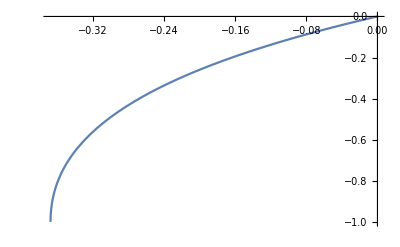

```mathematica
(*062419-5-ProductLog figure*)
Plot[ProductLog[x],{x,-1.0/E,0}]
```

```mathematica
D[P*P*P-P*P,P,P]
```

-2+6 P

```mathematica
(*092320-single variable Pijt Convex proof-no U no W with a,b*)
fa= D[d*P/(1+Exp[-n*c+m*P+b-a]),P,P]
```

-(2 d ⅇ^(-a+b-c n+m P) m)/((1+ⅇ^(-a+b-c n+m P))^2)+(2 d ⅇ^(-2 a+2 b-2 c n+2 m P) m^2 P)/((1+ⅇ^(-a+b-c n+m P))^3)-(d ⅇ^(-a+b-c n+m P) m^2 P)/((1+ⅇ^(-a+b-c n+m P))^2)

```mathematica
fa'=Simplify[fa,d≥0 && P>0 &&n>0 &&m>0 &&a>0&&b>0]
```

(d ⅇ^(a+b+c n+m P) m (ⅇ^(b+m P) (-2+m P)-ⅇ^(a+c n) (2+m P)))/((ⅇ^(a+c n)+ⅇ^(b+m P))^3)

```mathematica
NMaximize[{fa',d≥0 && P≥0 &&n>0 &&m>0&&c>0 &&a>0 &&b>0},{d,P,n,m,c,a,b}]
```

{-1.01803×10^-11,{d→0.0000127604,P→2.49715,n→0.868331,m→1.75168×10^-6,c→0.621222,a→0.308803,b→0.23252}}

```mathematica
NMaximize[{fa',d≥0&& P≥0 &&n==0.02 &&m==0.04&&c>0 &&a>0 &&b>0},{d,P,n,m,c,a,b}]
```

{0.,{d→0.,P→0.033699,n→0.02,m→0.04,c→0.0409664,a→3.54339,b→3.54219}}

```mathematica
NMinimize[{fa',d≥0 && P>0 &&n>0 &&m>0&&c>0 &&a>0 &&b>0},{d,P,n,m,c,a,b}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-25124.4,{d→38.0712,P→6.47363,n→14.6053,m→32.2904,c→13.764,a→35.3195,b→26.0374}}

```mathematica
NMinimize[{fa',d≥0 && P>0 &&n==0.02 &&m==0.04&&c>0 &&a>0 &&b>0},{d,P,n,m,c,a,b}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-57497.1,{d→121144.,P→2995.72,n→0.02,m→0.04,c→11816.9,a→0.0153371,b→115.225}}

```mathematica
(*092320-single variable Pijt Convex proof-no U no W no ab*)
fz= D[d*P/(1+Exp[-n*c+m*P]),P,P]
```

-(2 d ⅇ^(-c n+m P) m)/((1+ⅇ^(-c n+m P))^2)+(2 d ⅇ^(-2 c n+2 m P) m^2 P)/((1+ⅇ^(-c n+m P))^3)-(d ⅇ^(-c n+m P) m^2 P)/((1+ⅇ^(-c n+m P))^2)

```mathematica
fz'=Simplify[fz]
```

(d ⅇ^(c n+m P) m (ⅇ^(m P) (-2+m P)-ⅇ^(c n) (2+m P)))/((ⅇ^(c n)+ⅇ^(m P))^3)

```mathematica
fz''=Simplify[fz,d≥0 && P≥0 &&n>0 &&m>0 ]
```

(d ⅇ^(c n+m P) m (ⅇ^(m P) (-2+m P)-ⅇ^(c n) (2+m P)))/((ⅇ^(c n)+ⅇ^(m P))^3)

```mathematica
(*concavity*)
```

```mathematica
NMaximize[{Exp[m*P]*(m P-2)-Exp[c n]*(2+m P),d==100 && P≥0 &&n==0.02 &&m==0.04&&c==20 },{d,P,n,m,c}]
```

{-4.98365,{d→100.,P→0.,n→0.02,m→0.04,c→20.}}

```mathematica
NMaximize[{Exp[m*P]*(m P-2)-Exp[c n]*(2+m P),d≥0 && P≥0 &&n==0.02 &&m==0.04&&c≥0 },{d,P,n,m,c}]
```

{-4.,{d→1.5968,P→0.,n→0.02,m→0.04,c→0.}}

```mathematica
NMaximize[{Exp[m*P]*(m P-2)-Exp[c n]*(2+m P),d≥0 && P≥0 &&P<100&&n>0 &&m>0&&c>0 },{d,P,n,m,c}]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{4.80895236884971×10^1042,{d→19.7529,P→73.9737,n→21.0356,m→32.3505,c→19.6067}}

```mathematica
NMaximize[{fz'',d==100 && P≥0 &&n==0.02 &&m==0.04&&c==20 },{d,P,n,m,c}]
```

{-1.92209,{d→100.,P→-3.1958×10^-17,n→0.02,m→0.04,c→20.}}

```mathematica
NMaximize[{fz'',d≥0 && P≥0 &&n==0.02 &&m==0.04&&c≥0 },{d,P,n,m,c}]
```

{0.,{d→0.,P→0.69961,n→0.02,m→0.04,c→1.8888}}

```mathematica
NMaximize[{fz'',d≥0 && P≥0 &&P<100&&n>0 &&m>0&&c>0 },{d,P,n,m,c}]
```

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{1013.61,{d→6.1711,P→32.0369,n→11.4811,m→7.37694,c→20.4788}}

```mathematica
(*convexity*)
```

```mathematica
NMinimize[{Exp[m*P]*(m P-2)-Exp[c n]*(2+m P),d==100 && P≥0 &&n==0.02 &&m==0.04,c==20 },{d,P,n,m,c}]
```

{-7.50684,{d→100.,P→34.4148,n→0.02,m→0.04,c→20.}}

```mathematica
NMinimize[{fz'',d==100 && P≥0 &&n==0.02 &&m==0.04,c==20 },{d,P,n,m,c}]
```

{-2.00996,{d→100.,P→7.51239,n→0.02,m→0.04,c→20.}}

```mathematica
NMinimize[{fz'',d≥0 && P≥0 &&n>0 &&m>0,c>0 },{d,P,n,m,c}]
```

NMinimize::cvdiv: Failed to converge to a solution. The function may be unbounded.

{-189862.,{d→187.631,P→5.33084,n→2.20179,m→44.0949,c→107.345}}

```mathematica
(*092320-single variable Pijt Convex proof*)
fy=D[(Subscript[P, i,j^(t)]*Subscript[d, i,j^(t)])/( 1+Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]-ProductLog[(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]]]),Subscript[P, i,j^(t)],Subscript[P, i,j^(t)]]
```

-(2 ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])) d_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)+(2 ⅇ^(-2 ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-2 β_1 (-c_(i,j^t)+P_(i,j^t))-(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]))^2 d_(i,j^t) P_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3)-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]))^2 d_(i,j^t) P_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ((ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 β_1^2)/((1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3)-(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1^2)/((1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^2)) d_(i,j^t) P_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)

```mathematica
(*092320-single variable Pijt Convex proof-Logit*)
fy'=Simplify[fy,Subscript[P, i,j^(t)]≥0 && (*Subscript[U, i,j^(t)]>0 &&*) (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 (*&& Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]*)&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0]
```

(ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) β_1 (d_(i,j^t) (2 (1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))))+2 (1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2-(-1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) β_1 P_(i,j^t)+2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (2+β_1 P_(i,j^t)))+4 |T| β_2 U_(i,j^t)))/((1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3 (1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3)

```mathematica
(*092320-single variable Pijt Convex proof-Logit*)
fy''=FullSimplify[fy,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]≥0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]≥0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers]
```

(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 β_2 d_(i,j^t)^2 U_(i,j^t) (2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (2-β_1 P_(i,j^t)) U_(i,j^t)+2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t) (2+β_1 P_(i,j^t))+4 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^3)

```mathematica
(*092320-find global min-logit*)
NMinimize[{fy'',Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&(*BracketingBar[T]∈Integers*)(*BracketingBar[T]∈Integers*)(*Element[BracketingBar[T],Integers]*)(*&&*)-1/Exp[1]<(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]<0},{Subscript[P, i,j^t],Subscript[U, i,j^t],Subscript[c, i,j^t],Subscript[d, i,j^t],(*|T|*)BracketingBar[T],Subscript[β, 1],Subscript[β, 2]}]
```

NMinimize::nrnum: The function value 835.217-0.0407444 ⅈ is not a real number at {|T|,β_1,β_2,c_(i,j^t),d_(i,j^t),P_(i,j^t),U_(i,j^t)} = {1.35894,-2.73888,-0.519677,0.0593084,1.56415,1.58877,0.712428}.

{-1.28802,{P_(i,j^t)→0.539776,U_(i,j^t)→1.52732,c_(i,j^t)→0.266577,d_(i,j^t)→1.70775,|T|→1.51948,β_1→-1.7031,β_2→-0.0261128}}

```mathematica
(*092320-find global max-logit*)
NMaximize[{fy'',Subscript[P, i,j^(t)]≥4 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&(*BracketingBar[T]∈Integers*)(*BracketingBar[T]∈Integers*)(*Element[BracketingBar[T],Integers]*)(*&&*)-1/Exp[1]<(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]<0},{Subscript[P, i,j^t],Subscript[U, i,j^t],Subscript[c, i,j^t],Subscript[d, i,j^t],(*|T|*)BracketingBar[T],Subscript[β, 1],Subscript[β, 2]}]
```

NMaximize::nrnum: The function value 3.93797+0.0158184 ⅈ is not a real number at {|T|,β_1,β_2,c_(i,j^t),d_(i,j^t),P_(i,j^t),U_(i,j^t)} = {0.768963,-0.794827,-0.364025,0.0499525,0.540748,4.00618,0.178709}.

{0.157019,{P_(i,j^t)→4.90225,U_(i,j^t)→0.254329,c_(i,j^t)→1.97468,d_(i,j^t)→1.31231,|T|→0.840501,β_1→-1.07276,β_2→-0.0177158}}

```mathematica
(*061919-single variable Uijt Convex proof*)
fx=D[(Subscript[P, i,j^(t)]*Subscript[d, i,j^(t)])/( 1+Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]-ProductLog[(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]]]),Subscript[U, i,j^(t)],Subscript[U, i,j^(t)]]
```

(2 ⅇ^(-2 ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-2 β_1 (-c_(i,j^t)+P_(i,j^t))-(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t)))^2)/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t)))^2)/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) (-(2 ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2)/(d_(i,j^t)^2)+(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^3 β_2^3 U_(i,j^t))/(d_(i,j^t)^3)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))+(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t)^2)-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/((1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) U_(i,j^t))+(ⅇ^(2 β_1 (-c_(i,j^t)+P_(i,j^t))+(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 d_(i,j^t)^2 ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2))^2)/((|T|)^2 (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 β_2^2 U_(i,j^t)^2)-(ⅇ^(2 β_1 (-c_(i,j^t)+P_(i,j^t))+(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)^2 ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2))^2)/((|T|)^2 (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^2 β_2^2 U_(i,j^t)^2)))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2

```mathematica
(*061919-single variable Uijt Convex proof*)
fx'=Simplify[fx,Subscript[P, i,j^(t)]≥0 && (*Subscript[U, i,j^(t)]>0 &&*) (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 (*&& Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]*)&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0](*delete all Uijt criterias*)
```

-((ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) P_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t)) (2 ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 d_(i,j^t)+(2+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) |T| β_2 U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)-2 |T| β_2 U_(i,j^t))))/((1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3 (1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 d_(i,j^t) U_(i,j^t)^2))

```mathematica
(*062419-single variable Uijt Convex proof*)
fx''=FullSimplify[fx,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers]
```

-(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 P_(i,j^t))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 U_(i,j^t))

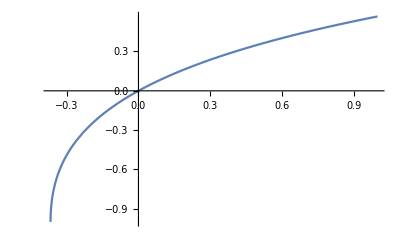

```mathematica
(*062019-ProductLog figure*)
Plot[ProductLog[x],{x,-1/E,1}]
```

```mathematica
f11=D[(Subscript[P, i,j^(t)]*Subscript[d, i,j^(t)])/( 1+Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]-ProductLog[(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]]]),Subscript[P, i,j^(t)],Subscript[P, i,j^(t)]]
```

-(2 ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])) d_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)+(2 ⅇ^(-2 ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-2 β_1 (-c_(i,j^t)+P_(i,j^t))-(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]))^2 d_(i,j^t) P_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3)-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]))^2 d_(i,j^t) P_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ((ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 β_1^2)/((1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3)-(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1^2)/((1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^2)) d_(i,j^t) P_(i,j^t))/((1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)

```mathematica
(*062019-Audit Simplify function*)
f11'=Simplify[f11,(*Subscript[P, i,j^(t)]>0 && Subscript[U, i,j^(t)]>0 && Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&& Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0*)Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]≥0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]≥0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0]
```

(ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) β_1 (d_(i,j^t) (2 (1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))))+2 (1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2-(-1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) β_1 P_(i,j^t)+2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (2+β_1 P_(i,j^t)))+4 |T| β_2 U_(i,j^t)))/((1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3 (1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3)

```mathematica
(*062419-Audit FullSimplify function*)
f11''=FullSimplify[f11,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers(*&&-1/Exp[1]<(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]<0*)]
```

(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 β_2 d_(i,j^t)^2 U_(i,j^t) (2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (2-β_1 P_(i,j^t)) U_(i,j^t)+2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t) (2+β_1 P_(i,j^t))+4 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^3)

```mathematica
f12=D[(Subscript[P, i,j^(t)]*Subscript[d, i,j^(t)])/( 1+Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]-ProductLog[(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]]]),Subscript[U, i,j^(t)],Subscript[P, i,j^(t)]]
```

-((ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)+(2 ⅇ^(-2 ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-2 β_1 (-c_(i,j^t)+P_(i,j^t))-(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 β_1 d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 β_2 U_(i,j^t))+(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^2 β_2 U_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) (-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_1 β_2)/(d_(i,j^t))+(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_1 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2

```mathematica
f12'=Simplify[f12,Subscript[P, i,j^(t)]>0 && Subscript[U, i,j^(t)]>0 && Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&& Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0]
```

(ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ((1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)^2+|T| β_2 U_(i,j^t) (d_(i,j^t) (2+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))-(1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) β_1 P_(i,j^t))+2 |T| β_2 U_(i,j^t))-ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 d_(i,j^t) (d_(i,j^t) (-2 (1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))))+(-1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) β_1 P_(i,j^t))-(1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t)))) |T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) (d_(i,j^t)+2 |T| β_2 (1+β_1 P_(i,j^t)) U_(i,j^t))))/((1+ⅇ^(ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]+β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3 (1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 d_(i,j^t) U_(i,j^t))

```mathematica
(*062419-Audit FullSimplify function*)
f12''=FullSimplify[f12,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers]
```

(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2)

```mathematica
f21=D[(Subscript[P, i,j^(t)]*Subscript[d, i,j^(t)])/( 1+Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]-ProductLog[(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]]]),Subscript[P, i,j^(t)],Subscript[U, i,j^(t)]]
```

-((ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2)+(2 ⅇ^(-2 ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-2 β_1 (-c_(i,j^t)+P_(i,j^t))-(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (-β_1+(ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1)/(1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 β_1 d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 β_2 U_(i,j^t))+(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^2 β_2 U_(i,j^t))))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2

```mathematica
(*062419-Audit FullSimplify function*)
f21''=FullSimplify[f21,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers]
```

(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2)

```mathematica
f22=D[(Subscript[P, i,j^(t)]*Subscript[d, i,j^(t)])/( 1+Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]-ProductLog[(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]]]),Subscript[U, i,j^(t)],Subscript[U, i,j^(t)]]
```

(2 ⅇ^(-2 ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-2 β_1 (-c_(i,j^t)+P_(i,j^t))-(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t)))^2)/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^3-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(|T| β_2)/(d_(i,j^t))-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t)))^2)/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2-(ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) d_(i,j^t) P_(i,j^t) (-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) (-(2 ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2)/(d_(i,j^t)^2)+(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^3 β_2^3 U_(i,j^t))/(d_(i,j^t)^3)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t))+(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/(|T| (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) β_2 U_(i,j^t)^2)-(ⅇ^(β_1 (-c_(i,j^t)+P_(i,j^t))+(|T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2)))/((1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]) U_(i,j^t))+(ⅇ^(2 β_1 (-c_(i,j^t)+P_(i,j^t))+(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 d_(i,j^t)^2 ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2))^2)/((|T|)^2 (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 β_2^2 U_(i,j^t)^2)-(ⅇ^(2 β_1 (-c_(i,j^t)+P_(i,j^t))+(2 |T| β_2 U_(i,j^t))/(d_(i,j^t))) ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)^2 ((ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2)/(d_(i,j^t))-(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) (|T|)^2 β_2^2 U_(i,j^t))/(d_(i,j^t)^2))^2)/((|T|)^2 (1+ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^2 β_2^2 U_(i,j^t)^2)))/(1+ⅇ^(-ProductLog[(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))))^2

```mathematica
(*062019-Audit FullSimplify function*)
f22''=FullSimplify[f22,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers]
```

-(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 P_(i,j^t))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 U_(i,j^t))

```mathematica
(*A={{-2,4},{1,-2}}
*B={{2,4},{-3,-6}}
*A.B
```

```mathematica
H={{f11'',f12''},{f21'',f22''}}
```

{{(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 β_2 d_(i,j^t)^2 U_(i,j^t) (2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (2-β_1 P_(i,j^t)) U_(i,j^t)+2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t) (2+β_1 P_(i,j^t))+4 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^3),(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2)},{(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2),-(|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 P_(i,j^t))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 U_(i,j^t))}}

```mathematica
M={u,v}.H.{u,v}
```

v (-(v |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 P_(i,j^t))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 U_(i,j^t))+(u |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2))+u ((v |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2)+(u |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 β_2 d_(i,j^t)^2 U_(i,j^t) (2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (2-β_1 P_(i,j^t)) U_(i,j^t)+2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t) (2+β_1 P_(i,j^t))+4 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^3))

```mathematica
(*062419-Fullsimplify M-Revise conditions*)
```

```mathematica
M'=FullSimplify[M,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers]
```

-((|T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 (v ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+(v |T| β_2+u β_1 d_(i,j^t)) U_(i,j^t)) (-2 u ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)^2 U_(i,j^t)+|T| β_2 (v |T| β_2 P_(i,j^t)+u d_(i,j^t) (-2+β_1 P_(i,j^t))) U_(i,j^t)^2-ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t) U_(i,j^t) (u d_(i,j^t) (2+β_1 P_(i,j^t))-2 |T| β_2 (v P_(i,j^t)-2 u U_(i,j^t)))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 d_(i,j^t) (-2 u |T| β_2 U_(i,j^t)^2+d_(i,j^t) (v P_(i,j^t)-2 u (2+β_1 P_(i,j^t)) U_(i,j^t)))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 U_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^3))

```mathematica
(*062419-u,v find global min-ok-keep*)
NMinimize[{M',Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&(*BracketingBar[T]∈Integers*)(*BracketingBar[T]∈Integers*)(*Element[BracketingBar[T],Integers]*)(*&&*)-1/Exp[1]<(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]<0&&u≠0&&v≠0},{Subscript[P, i,j^t],Subscript[U, i,j^t],Subscript[c, i,j^t],Subscript[d, i,j^t],(*|T|*)BracketingBar[T],Subscript[β, 1],Subscript[β, 2],u,v}]
```

NMinimize::nrnum: The function value 7.07544-0.21304 ⅈ is not a real number at {u,v,|T|,β_1,β_2,c_(i,j^t),d_(i,j^t),P_(i,j^t),U_(i,j^t)} = {0.108373,-0.856192,2.29467,-0.821546,-1.09541,0.58085,2.15228,0.118449,1.07715}.

{-4.39405,{P_(i,j^t)→1.02076,U_(i,j^t)→0.163945,c_(i,j^t)→1.05533,d_(i,j^t)→1.12473,|T|→1.40115,β_1→-0.434159,β_2→-0.876411,u→0.573088,v→0.727618}}

```mathematica
(*062419-u,v find global min-test*)
NMinimize[{M',Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&BracketingBar[T]∈Integers&&-1/Exp[1]<(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]<0&&u≠0&&v≠0},{Subscript[P, i,j^t],Subscript[U, i,j^t],Subscript[c, i,j^t],Subscript[d, i,j^t],BracketingBar[T],Subscript[β, 1],Subscript[β, 2],u,v}]
```

NMinimize::nrnum: The function value 13543.5-0.113761 ⅈ is not a real number at {u,v,|T|,β_1,β_2,c_(i,j^t),d_(i,j^t),P_(i,j^t),U_(i,j^t)} = {0.0380313,-0.803018,1.98291,-0.314201,-1.80059,1.12204,1.81441,0.951561,1.65276}.

{-88.7519,{P_(i,j^t)→1.13271,U_(i,j^t)→0.0381169,c_(i,j^t)→0.314559,d_(i,j^t)→0.711762,|T|→2.53442,β_1→-0.0563882,β_2→-1.16833,u→-0.0192504,v→-0.881291}}

```mathematica
(*062419-u,v find global min-try minimize-fail*)P
Minimize[{M,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&(*BracketingBar[T]∈Integers*)BracketingBar[T]∈Integers&&-1/Exp[1]<(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]<0&&u≠0&&v≠0},{Subscript[P, i,j^t],Subscript[U, i,j^t],Subscript[c, i,j^t],Subscript[d, i,j^t],(*|T|*)BracketingBar[T],Subscript[β, 1],Subscript[β, 2],u,v}]
```

Minimize::mixdom: Exact optimization with mixed real and integer variables is not yet implemented.

Minimize[{v (-(v |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 P_(i,j^t))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 U_(i,j^t))+(u |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2))+u ((v |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_2 d_(i,j^t) (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (1-β_1 P_(i,j^t)) U_(i,j^t)+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t)+2 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^2)+(u |T| ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] β_1 β_2 d_(i,j^t)^2 U_(i,j^t) (2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^3 d_(i,j^t)+|T| β_2 (2-β_1 P_(i,j^t)) U_(i,j^t)+2 ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))]^2 (d_(i,j^t) (2+β_1 P_(i,j^t))+|T| β_2 U_(i,j^t))+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] (d_(i,j^t) (2+β_1 P_(i,j^t))+4 |T| β_2 U_(i,j^t))))/((1+ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))])^3 (ProductLog[(ⅇ^(β_1 (c_(i,j^t)-P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))] d_(i,j^t)+|T| β_2 U_(i,j^t))^3)),P_(i,j^t)≥0&&U_(i,j^t)>0&&c_(i,j^t)>0&&d_(i,j^t)>0&&U_(i,j^t)≤d_(i,j^t)&&β_1<0&&β_2<0&&|T|>0&&|T|∈ℤ&&-1/ⅇ<(ⅇ^(-β_1 (-c_(i,j^t)+P_(i,j^t))-(|T| β_2 U_(i,j^t))/(d_(i,j^t))) |T| β_2 U_(i,j^t))/(d_(i,j^t))<0&&u≠0&&v≠0},{P_(i,j^t),U_(i,j^t),c_(i,j^t),d_(i,j^t),|T|,β_1,β_2,u,v}]

```mathematica
(*062419-u,v find global min-try findminimize-fail*)
FindMinimum[{M,Subscript[P, i,j^(t)]≥0 && Subscript[U, i,j^(t)]>0 && (*Subscript[P, i,j^(t)]>Subscript[c, i,j^(t)]&&*) Subscript[c, i,j^(t)]>0 && Subscript[d, i,j^(t)]>0 && Subscript[U, i,j^(t)]≤Subscript[d, i,j^(t)]&& Subscript[β, 1]<0&& Subscript[β, 2]<0&&BracketingBar[T]>0&&(*BracketingBar[T]∈Integers*)BracketingBar[T]∈Integers&&-1/Exp[1]<(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]*Exp[-Subscript[β, 1]*(Subscript[P, i,j^(t)]-Subscript[c, i,j^(t)])-(Subscript[β, 2]*BracketingBar[T]*Subscript[U, i,j^(t)])/Subscript[d, i,j^(t)]]<0&&u≠0&&v≠0},{Subscript[P, i,j^t],Subscript[U, i,j^t],Subscript[c, i,j^t],Subscript[d, i,j^t],(*|T|*)BracketingBar[T],Subscript[β, 1],Subscript[β, 2],u,v}]
```

FindMinimum::eqineq: Constraints in {|T|∈,|T|>0,c_(i,j^t)>0,d_(i,j^t)>0,U_(i,j^t)>0,P_(i,j^t)≥0,-1/ⅇ<(ⅇ^(-β_1 (Times[«2»]+Subscript[«3»])-(|T| β_2 U_(«1»))/Subscript[«3»]) |T| β_2 U_(i,j^t))/(d_(i,j^t)),β_1<0,β_2<0,(ⅇ^(-β_1 (Times[«2»]+Subscript[«3»])-(|T| β_2 U_(i,«1»))/Subscript[«3»]) |T| β_2 U_(i,j^t))/(d_(i,j^t))<0,U_(i,j^t)≤d_(i,j^t),u≠0,v≠0} are not all equality or inequality constraints. With the exception of integer domain constraints for linear programming, domain constraints or constraints with Unequal (!=) are not supported.

FindMinimum[{M,P_(i,j^t)≥0&&U_(i,j^t)>0&&c_(i,j^t)>0&&d_(i,j^t)>0&&U_(i,j^t)≤d_(i,j^t)&&β_1<0&&β_2<0&&|T|>0&&|T|∈ℤ&&-1/Exp[1]<((β_2 |T| U_(i,j^t)) Exp[-β_1 (P_(i,j^t)-c_(i,j^t))-(β_2 |T| U_(i,j^t))/(d_(i,j^t))])/(d_(i,j^t))<0&&u≠0&&v≠0},{P_(i,j^t),U_(i,j^t),c_(i,j^t),d_(i,j^t),|T|,β_1,β_2,u,v}]

```mathematica
(*062419-quote above for ProductLog value*)
f2[a_,b_,U_,d_,T_,P_,c_]:=(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d]
ProductLog[f2[-0.4341594882951717,-0.8764114822484739,0.1639447282384795,1.1247291487181463,1.4011463242647808,1.0207570912096275,1.0553324803756834]]
```

-0.278664

```mathematica
M''=.
```

```mathematica
2*Exp[-2.5]
```

0.16417

```mathematica
-Exp[-1.0]
```

-0.367879

```mathematica
(*062119-ProductLog special value calculate*)
f[a_,b_,U_,d_,T_,P_,c_]:=(b*T*U)/d*Exp[-a*(P-c)-(b*T*U)/d]
```

```mathematica
f[-1.0,-1,1,2,1,1,2]
```

-0.303265

```mathematica
ProductLog[-0.3032653298563167]
```

-0.5

```mathematica
{{a,b},{c,d}}.{x,y}
```

{a x+b y,c x+d y}

```mathematica
{x,y}.{{a,b},{c,d}}
```

{a x+c y,b x+d y}

```mathematica
Solve[a x^2+b x+c==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

```mathematica
Reduce[a x^2+b x+c==0,x]
```

(a≠0&&(x==(-b-√(b^2-4 a c))/(2 a)||x==(-b+√(b^2-4 a c))/(2 a)))||(a==0&&b≠0&&x==-c/b)||(c==0&&b==0&&a==0)

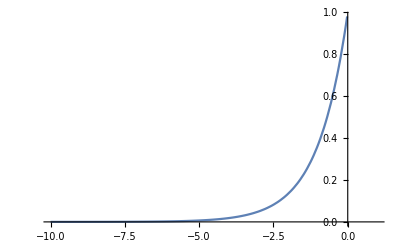

```mathematica
Plot[Exp[x],{x,-10,1}]
```

```mathematica
eqn={(a x - 1)  b ==  Exp[c x],a>0,b>0,c>0}
```

```mathematica
Reduce[eqn,x]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

```mathematica
Reduce[{b (-1+a x)==ⅇ^(c x)},x,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{b (-1+a x)==ⅇ^(c x)},x,ℝ]

```mathematica
Reduce[a x - b == Exp[c x],x,Reals]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[-b+a x==ⅇ^(c x),x,ℝ]

```mathematica
Reduce[{(a*x - 1)*b ==  Exp[c*x]},x]
```

(C[1]∈ℤ&&((c≠0&&a b≠0&&x==(c-a ProductLog[C[1],-(c ⅇ^(c/a))/(a b)])/(a c))||(b≠0&&c≠0&&a==0&&x==(2 ⅈ π C[1]+Log[-b])/c)))||(b==-1&&x==0)||(a==0&&b==-1&&c==0)||(a b≠0&&c==0&&x==(1+b)/(a b))

```mathematica
(*060619-1st edition solve Lambert *)
Reduce[{Exp[c*x]-a*x*b+b ==0},x]
```

(C[1]∈ℤ&&((c≠0&&a b≠0&&x==(c-a ProductLog[C[1],-(c ⅇ^(c/a))/(a b)])/(a c))||(b≠0&&c≠0&&a==0&&x==(2 ⅈ π C[1]+Log[-b])/c)))||(b==-1&&x==0)||(a==0&&b==-1&&c==0)||(a b≠0&&c==0&&x==(1+b)/(a b))

```mathematica
Reduce[a^2<1&&y-Sqrt[a]==0,y(*,Reals*)]
```

-1<a<1&&y==√a

```mathematica
(*061419 10am-1st edition add Reals*)
Reduce[{Exp[c*x]-a*x*b+b ==0(*,a>0,b>0,c>0*)},x]
```

(C[1]∈ℤ&&((c≠0&&a b≠0&&x==(c-a ProductLog[C[1],-(c ⅇ^(c/a))/(a b)])/(a c))||(b≠0&&c≠0&&a==0&&x==(2 ⅈ π C[1]+Log[-b])/c)))||(b==-1&&x==0)||(a==0&&b==-1&&c==0)||(a b≠0&&c==0&&x==(1+b)/(a b))

```mathematica
(*061619 9am-1st edition add Reals*)
Reduce[{Exp[c*x]-a*x*b+b ==0,ab>0,ac>0,bc>0},x]
```

(b==-1&&ab>0&&ac>0&&bc>0&&x==0)||(a==0&&b==-1&&c==0&&ab>0&&ac>0&&bc>0)||(a b≠0&&c==0&&ab>0&&ac>0&&bc>0&&x==(1+b)/(a b))||(C[1]∈ℤ&&c≠0&&a b≠0&&ab>0&&ac>0&&bc>0&&x==(c-a ProductLog[C[1],-(c ⅇ^(c/a))/(a b)])/(a c))||(C[1]∈ℤ&&b≠0&&c≠0&&a==0&&ab>0&&ac>0&&bc>0&&x==(2 ⅈ π C[1]+Log[-b])/c)

```mathematica
(*061419 6am-2nd edition verify Wijt solution*)
```

```mathematica
Reduce[{Exp[-b*x]-d*1/T*1/U*Exp[a*(P-c)]*x+Exp[a*(P-c)]==0},x(*,Reals*)]
```

(C[1]∈ℤ&&((T U≠0&&ⅇ^(a (-c+P))≠0&&b≠0&&d==0&&x==(2 ⅈ π C[1]+Log[-ⅇ^(-a (-c+P))])/b)||(ⅇ^(a (-c+P))≠0&&b≠0&&d≠0&&T U≠0&&x==(b T U+d ProductLog[C[1],(b ⅇ^(-a (-c+P)-(b T U)/d) T U)/d])/(b d))))||(b==0&&((d ⅇ^(a (-c+P))≠0&&T U≠0&&x==(ⅇ^(-a (-c+P)) (1+ⅇ^(a (-c+P))) T U)/d)||(T U≠0&&d==0&&ⅇ^(a (-c+P))==-1)))||(T U≠0&&ⅇ^(a (-c+P))==-1&&x==0)

```mathematica
Reduce[{Exp[-b*x]-d*1/T*1/U*Exp[a*(P-c)]*x+Exp[a*(P-c)]==0,b<0,d≥0,T>0,U>0,a<0,P>0,c>0},x(*,Reals*)]
```

(a<0&&b<0&&c>0&&d>0&&P>0&&T>0&&U>0&&x==(b T U+d ProductLog[C[1],(b ⅇ^(a (c-P)-(b T U)/d) T U)/d])/(b d))||(C[1]∈ℤ&&a<0&&b<0&&c>0&&d==0&&P>0&&T>0&&U>0&&x==-(-a c+a P-ⅈ π-2 ⅈ π C[1])/b)

```mathematica
Reduce[{Exp[-b*x]-d*1/T*1/U*Exp[a*(P-c)]*x+Exp[a*(P-c)]==0,b<0,d≥0,T>0,U>0,a<0,P>0,c>0},x,Reals]
```

Reduce[{ⅇ^(a (-c+P))+ⅇ^(-b x)-(d ⅇ^(a (-c+P)) x)/(T U)==0,b<0,d≥0,T>0,U>0,a<0,P>0,c>0},x,ℝ]

```mathematica
(*061419-2nd edition verify Wijt using Real function*)
```

```mathematica
Reduce[{Exp[-b*x]-d*1/T*1/U*Exp[a*(P-c)]*x+Exp[a*(P-c)]==0},x,Reals]
```

```mathematica
(*061719-simulation for ProductLog*)
ProductLog[0,-0.1]
```

-0.111833

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot3D[10*x/(1+Exp[(x-1)+y-ProductLog[Exp[x-1+y]]]),{x,0,4},{y,0,0.5},RegionFunction->Function[{x,y,z},y*Exp[x-1+y]<Exp[-1] && x>1 && y<10],ColorFunction->Function[{x,y,z},Hue[z]],AxesLabel->{"Pricing","Unmet Demand","f(x)"}]
```

-Graphics3D-

```mathematica
Plot3D[x+y,{x,0,2},{y,0,2},ColorFunction->Function[{x,y,z},Hue[z]]]
```

-Graphics3D-

```mathematica
ContourPlot3D[16 x^3+16 y^3-31 z^3+24 x^2 z-48 x^2 y-48 x y^2+24 y^2 z-93.5307 z^2-72 z==0,{x,-2,2},{y,-2,2},{z,-2.3,2},ColorFunction->Function[{x,y,z,f},ColorData["Rainbow"][z]],Mesh->4]

ContourPlot[-15000*x * y / (-150 * y-100),{x,0,5000},{y,0,100},ColorFunction->"Rainbow"]
```

-Graphics3D-

```mathematica
Plot3D[10*x/(1+Exp[(x-1)+y-ProductLog[Exp[x-1+y]]]),{x,-3,3},{y,-2,2}]

ContourPlot3D[z==10*x/(1+Exp[(x-1)+y-ProductLog[Exp[x-1+y]]]),{x,-3,3},{y,-2,2},ColorFunction->Function[{x,y,z,f},ColorData["Rainbow"][z]],Mesh->4]
```

-Graphics3D-

ContourPlot3D::argrx: ContourPlot3D called with 3 arguments; 4 arguments are expected.

ContourPlot3D[z==(10 x)/(1+Exp[(x-1)+y-ProductLog[Exp[x-1+y]]]),{x,-3,3},{y,-2,2},ColorFunction→Function[{x,y,z,f},ColorData[Rainbow][z]],Mesh→4]

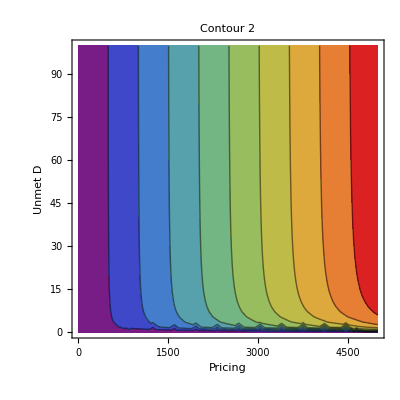

```mathematica
Show[%59,FrameLabel->{{HoldForm[Unmet D],None},{HoldForm[Pricing],None}},PlotLabel->HoldForm[Contour 2],LabelStyle->{GrayLevel[0]}]
```

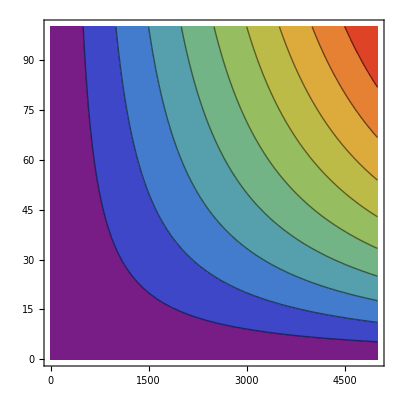

```mathematica
ContourPlot[-100*x * y / (-1 * y-100),{x,0,5000},{y,0,100},ColorFunction->"Rainbow"]
```

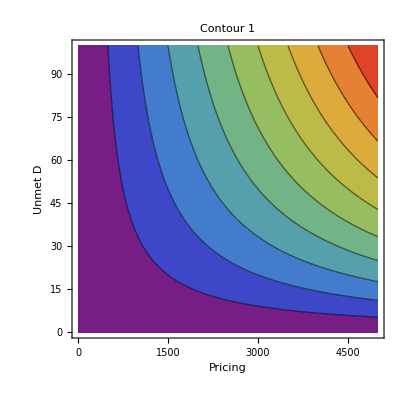

```mathematica
Show[%60,FrameLabel->{{HoldForm[Unmet D],None},{HoldForm[Pricing],None}},PlotLabel->HoldForm[Contour 1],LabelStyle->{GrayLevel[0]}]
```

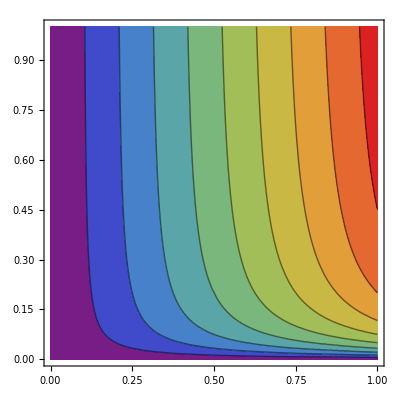

```mathematica
ContourPlot[-500*x * y / (-100 * y-5),{x,0,1},{y,0,1},ColorFunction->"Rainbow"]
```

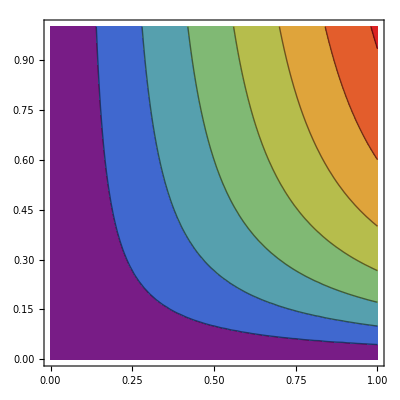

```mathematica
ContourPlot[-10*x * y / (-5 * y-2),{x,0,1},{y,0,1},ColorFunction->"Rainbow"]
```

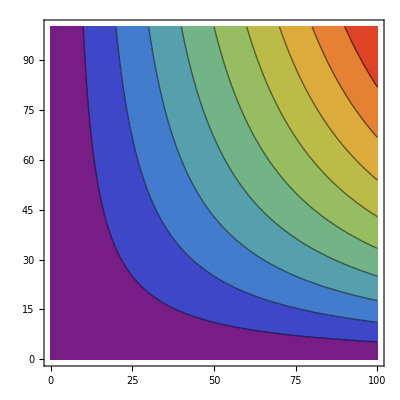

```mathematica
ContourPlot[-1000*x * y / (-10 * y-1000),{x,0,100},{y,0,100},ColorFunction->"Rainbow"]
```

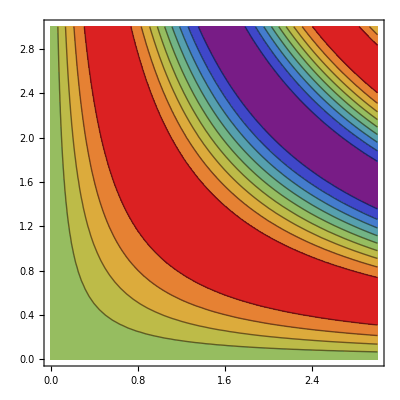

```mathematica
ContourPlot[Sin[x y],{x,0,3},{y,0,3},ColorFunction->"Rainbow"]
```

```mathematica
sd
```

Set::write: Tag In in In[1] is Protected.

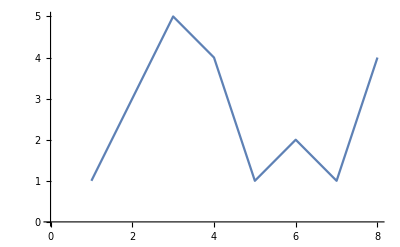

```mathematica
In[1]=ListLinePlot[{1,3,5,4,1,2,1,4}]
```

Set::write: Tag In in In[2] is Protected.

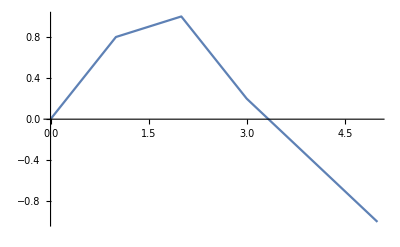

```mathematica
In[2]=ListLinePlot[{{0,0},{1,0.8},{2,1},{3,0.2},{4,-0.4},{5,-1}}]
```

```mathematica
Show[%6,AxesLabel->{HoldForm[(In[2]=ListLinePlot[{{0,0},{1,0.8},{2,1},{3,0.2},{4,-0.4},{5,-1}}]) of Oranges],HoldForm[Utility]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

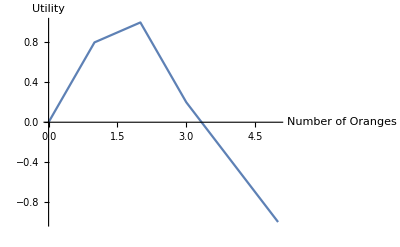

```mathematica
Show[%7,AxesLabel->{HoldForm[Number of Oranges],HoldForm[Utility]},PlotLabel->None]
```

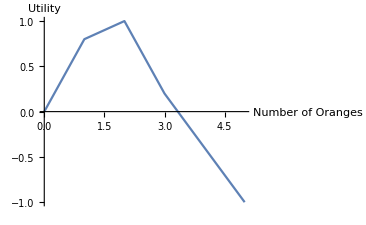

```mathematica
Show[%12,Background->White]
```

Set::write: Tag In in In[3] is Protected.

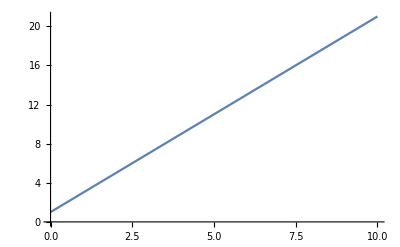

```mathematica
In[3]=Plot[2x+1,{x,0,10}]
```

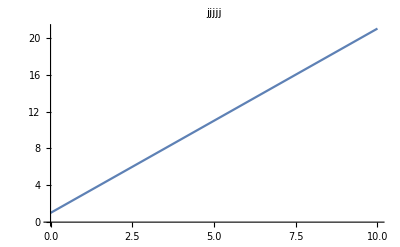

```mathematica
Show[%19,PlotLabel->HoldForm[jjjjj],LabelStyle->{GrayLevel[0]}]
```

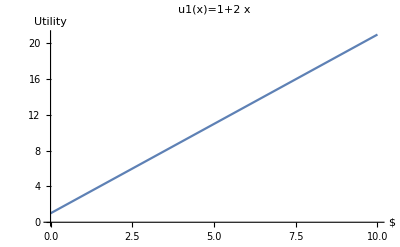

```mathematica
Show[%20,AxesLabel->{HoldForm[$],HoldForm[Utility]},PlotLabel->HoldForm[u1[x]=1+2 x]]
```

```mathematica
Show[%20,Axes->False]
```

```mathematica
In[4]=Plot[x^2,{x,0,10}]
```

Set::write: Tag In in In[4] is Protected.

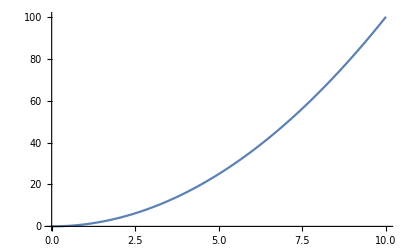
```mathematica
-Graphics-

In[11]=Plot[0.02504+0.01437*x-0.002030*x^2,{x,0,10}]
```

-Graphics-

Set::write: Tag In in In[11] is Protected.

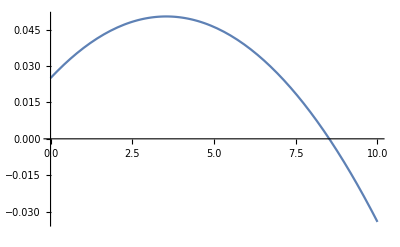

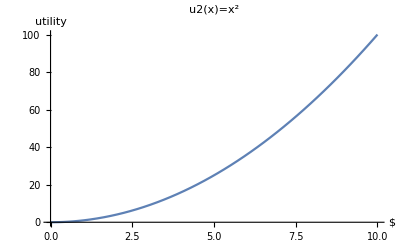

```mathematica
Show[%23,AxesLabel->{HoldForm[$],HoldForm[utility]},PlotLabel->HoldForm[u2[x]=x^2],LabelStyle->{GrayLevel[0]}]
```

Set::write: Tag In in In[5] is Protected.

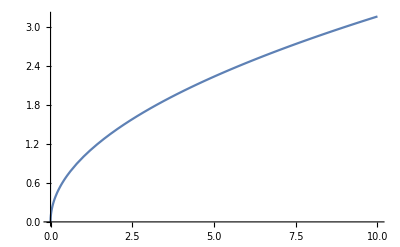

```mathematica
In[5]=Plot[x^(1/2),{x,0,10}]
```

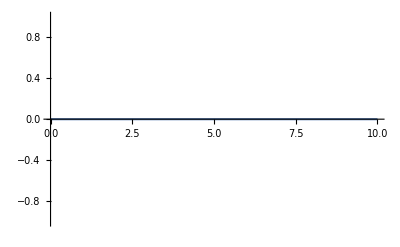

```mathematica
Plot[0,{x,0,10}]
```

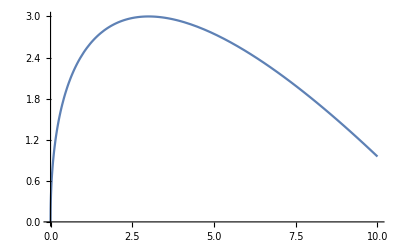

```mathematica
Plot[(12*x)^(1/2)-x,{x,0,10}]
```

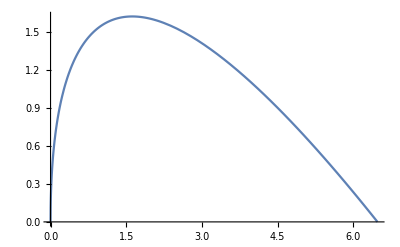

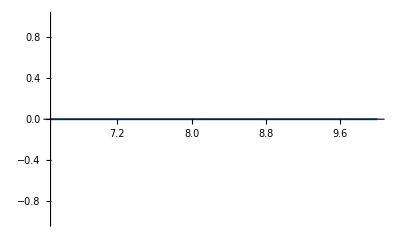

```mathematica
p1=Plot[(6.48*x)^(1/2)-x,{x,0,6.48}]
p2=Plot[0,{x,6.48,10}]
```

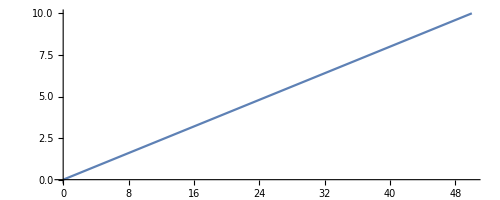

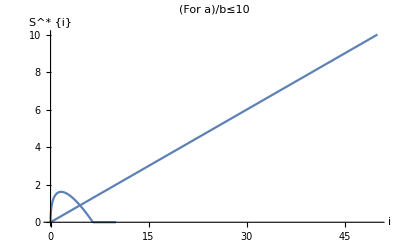

```mathematica
t1=ParametricPlot[{y*5,y},{y,0,10}]

Show [Plot[y=(6.48*x)^(1/2)-x,{x,0,6.48}],Plot[y=0,{x,6.48,10}],t1,PlotRange -> Automatic,AxesLabel->{HoldForm[i],HoldForm[SuperStar[S]{i}]},PlotLabel->HoldForm[For a/b  <=10],LabelStyle->{GrayLevel[0]}]
```

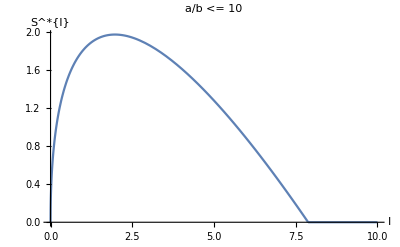

```mathematica
a=Show [Plot[(7.88*x)^(1/2)-x,{x,0,7.88}],Plot[0,{x,7.88,10}],PlotRange -> Automatic,AxesLabel->{HoldForm["I"],HoldForm["S^*{I}"]},PlotLabel->HoldForm["a/b <= 10"],LabelStyle->{GrayLevel[0]}]
```

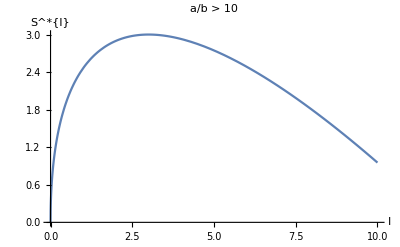

```mathematica
b=Show [Plot[(12*x)^(1/2)-x,{x,0,10}],PlotRange -> Automatic,AxesLabel->{HoldForm["I"],HoldForm["S^*{I}"]},PlotLabel->HoldForm[ "a/b > 10"],LabelStyle->{GrayLevel[0]}]
```

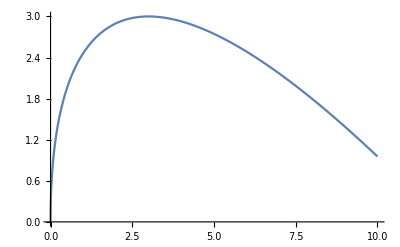

```mathematica
b1=Plot[(12*x)^(1/2)-x,{x,0,10},PlotRange -> Automatic]
```

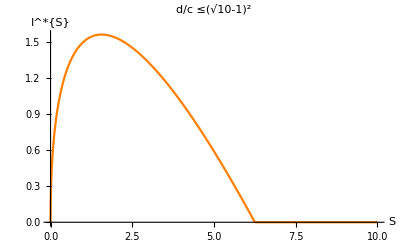

```mathematica
c=Show [Plot[y^(1/2)+(2.25*y)^(1/2)-y,{y,0,6.25},PlotStyle->Orange],Plot[0,{y,6.25,10},PlotStyle->Orange],PlotRange -> Automatic,AxesLabel->{HoldForm["S"],HoldForm["I^*{S}"]},PlotLabel->HoldForm["d/c  ≤(√10-1)^2"],LabelStyle->{GrayLevel[0]}]
```

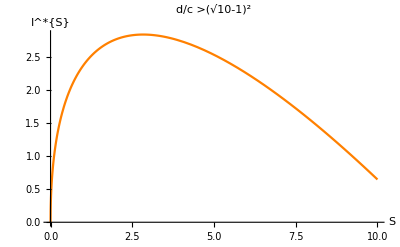

```mathematica
d=Show [Plot[y^(1/2)+(5.6*y)^(1/2)-y,{y,0,10},PlotStyle->Orange],AxesLabel->{HoldForm["S"],HoldForm["I^*{S}"]},PlotLabel->HoldForm["d/c  >(√10-1)^2"],LabelStyle->{GrayLevel[0]}]
```

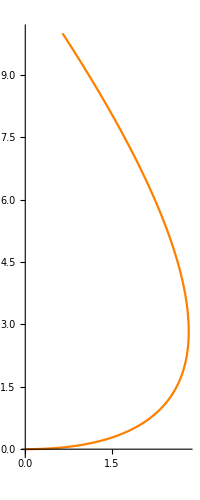

```mathematica
d1=ParametricPlot[{y^(1/2)+(5.6*y)^(1/2)-y,y},{y,0,10},PlotStyle->Orange]
```

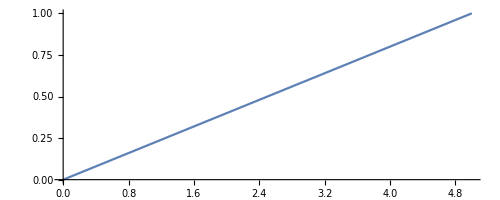

```mathematica
t2=ParametricPlot[{y*5,y},{y,0,1}]
```

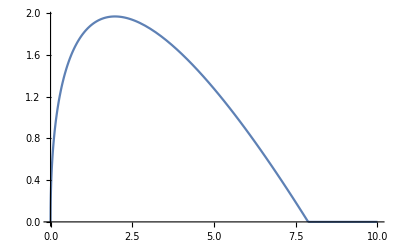

```mathematica
a1=Show [Plot[(7.88*x)^(1/2)-x,{x,0,7.88}],Plot[0,{x,7.88,10}],PlotRange -> All]
```

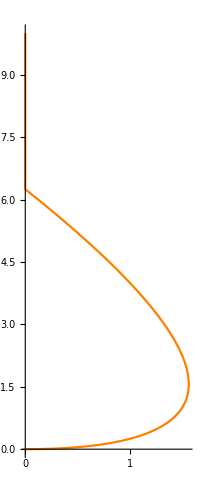

```mathematica
c1=Show[ParametricPlot[{y^(1/2)+(2.25*y)^(1/2)-y,y},{y,0,6.25},PlotStyle->Orange],ParametricPlot[{0,y},{y,6.25,10},PlotStyle->Orange],PlotRange->All]
```

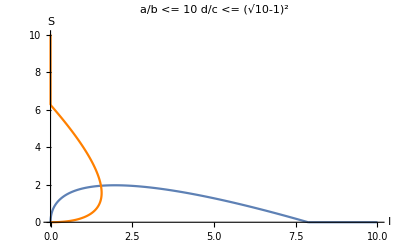

```mathematica
e=Show[a1,c1,PlotRange->All,AxesLabel->{HoldForm["I"],HoldForm["S"]},PlotLabel->HoldForm[ "a/b <= 10 
d/c <= (√10-1)^2"],LabelStyle->{GrayLevel[0]}]
```

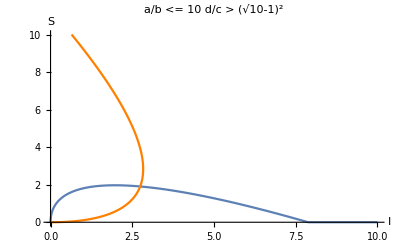

```mathematica
f=Show[a1,d1,PlotRange->All,AxesLabel->{HoldForm["I"],HoldForm["S"]},PlotLabel->HoldForm[ "a/b <= 10 
d/c > (√10-1)^2"],LabelStyle->{GrayLevel[0]}]
```

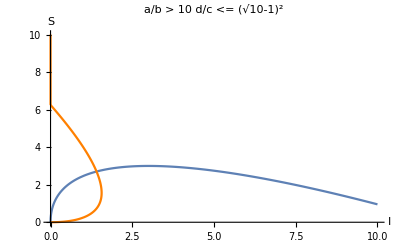

```mathematica
g=Show[b1,c1,PlotRange->All,AxesLabel->{HoldForm["I"],HoldForm["S"]},PlotLabel->HoldForm[ "a/b > 10 
d/c <= (√10-1)^2"],LabelStyle->{GrayLevel[0]}]
```

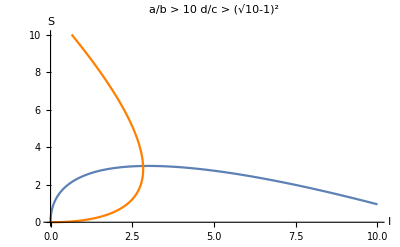

```mathematica
h=Show[b1,d1,PlotRange->All,AxesLabel->{HoldForm["I"],HoldForm["S"]},PlotLabel->HoldForm[ "a/b > 10 
d/c > (√10-1)^2"],LabelStyle->{GrayLevel[0]}]
```

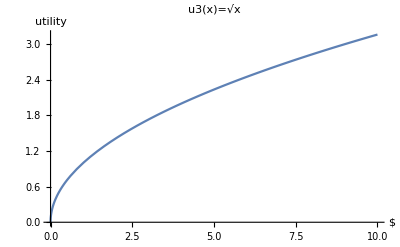

```mathematica
Show[%27,AxesLabel->{HoldForm[$],HoldForm[utility]},PlotLabel->HoldForm[u3[x]=√x],LabelStyle->{GrayLevel[0]}]
```

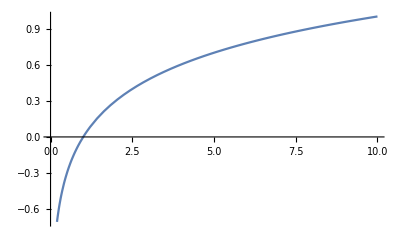

```mathematica
Plot[Log[10,x],{x,0,10}]
```

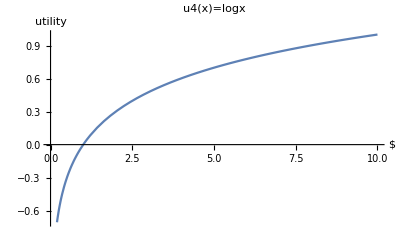

```mathematica
Show[%55,AxesLabel->{HoldForm[$],HoldForm[utility]},PlotLabel->HoldForm[u4[x]=logx],LabelStyle->{GrayLevel[0]}]
```

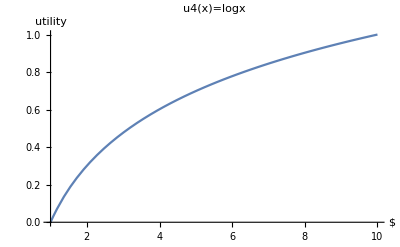

```mathematica
Show[%53,AxesLabel->{HoldForm[$],HoldForm[utility]},PlotLabel->HoldForm[u4[x]=logx],LabelStyle->{GrayLevel[0]}]
```

```mathematica
FindMaximum[{x^2y,x+2y≤10,x≥0,y≥0},{x,y}]
```

{74.0741,{x→6.66667,y→1.66667}}

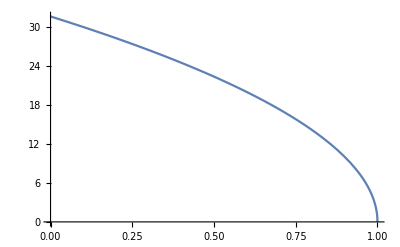

```mathematica
q1=Plot[(1000-1000*g)^(1/2),{g,0,1}]
```

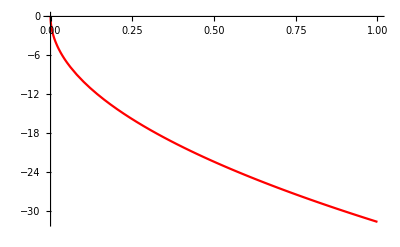

```mathematica
q2=Plot[-(1000*g)^(1/2),{g,0,1},PlotStyle->Red]
```

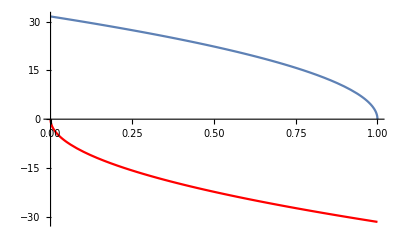

```mathematica
q3=Show[q1,q2,PlotRange->Automatic]
```

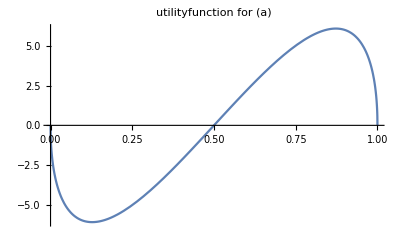

```mathematica
Plot[g*(1000-1000*g)^(1/2)-(1-g)*(1000*g)^(1/2),{g,0,1},PlotLabel->HoldForm["Utilityfunction for (a)"]]
```

```mathematica
FindMaximum[{g*(1000-1000*g)^(1/2)-(1-g)*(1000*g)^(1/2),0≤g≤1},{g,0.9}]
```

{6.08581,{g→0.872678}}

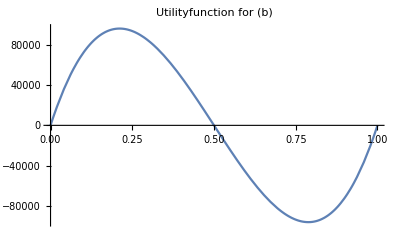

Show::gtype: Plus is not a type of graphics.

```mathematica
Plot[g*(1000-1000*g)^(2)-(1-g)*(1000*g)^(2),{g,0,1},PlotLabel->HoldForm["Utilityfunction for (b)"]]
```

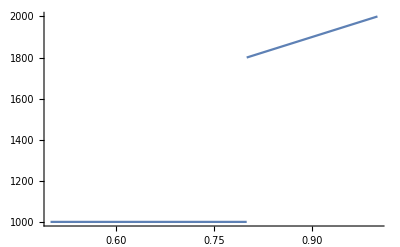

```mathematica
Show[Plot[1000,{g,0.5,0.8}],Plot[1000+1000*g,{g,0.8,1}],PlotRange -> Automatic]
```

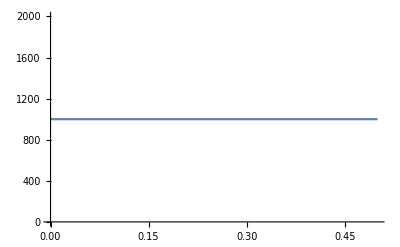

```mathematica
Plot[1000,{g,0,0.5}]
```

```mathematica
Show[ContourPlot[x^2y,{x,0,10},{y,0,5},RegionFunction->Function[{x,y},x+2 y≤10]],Graphics[{PointSize[0.03],Red,Point[{6.66667,1.66667}]}]]
```

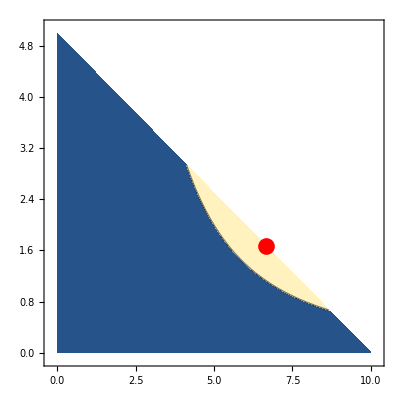

```mathematica
Show[Plot3D[x^2y,{x,0,10},{y,0,5},RegionFunction->Function[{x,y,z},x+2y≤10]],Graphics3D[{PointSize[0.03],Red,Point[{6.66667,1.66667,74.0741}]}]]
```

-Graphics3D-

```mathematica
FindMaximum[{2x+y,x+2y≤10,x≥0,y≥0},{x,y}]
```

{20.,{x→10.,y→0.}}

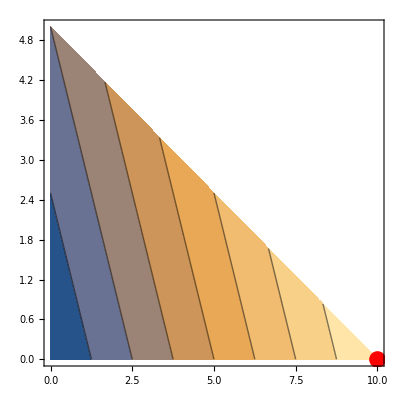

```mathematica
Show[ContourPlot[2x+y,{x,0,10},{y,0,5},RegionFunction->Function[{x,y},x+2 y≤10]],Graphics[{PointSize[0.03],Red,Point[{10,0}]}]]
```

```mathematica
Show[Plot3D[2x+y,{x,0,10},{y,0,5},RegionFunction->Function[{x,y,z},x+2y≤10]],Graphics3D[{PointSize[0.03],Red,Point[{10,0,20}]}]]
```

```mathematica
FindMaximum[{t,t≤x,t≤3y,x+2y≤10,x≥0,y≥0,t≥0},{x,y,t}]
```

{6.,{x→6.,y→2.,t→6.}}

```mathematica
Show[Plot3D[Min[{x,3y}],{x,0,10},{y,0,5},RegionFunction->Function[{x,y},x+2y≤10]],Graphics3D[{PointSize[0.03],Red,Point[{6,2,6}]}]]
```

-Graphics3D-

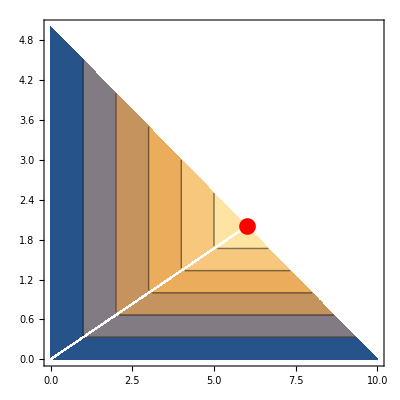

```mathematica
Show[ContourPlot[Min[{x,3y}],{x,0,10},{y,0,5},RegionFunction->Function[{x,y},x+2 y≤10]],Graphics[{PointSize[0.03],Red,Point[{6,2}]}]]
```

```mathematica
FindMaximum[50x/{x+1}-5x,{x,0}]
```

{23.3772,{x→2.16228}}

Set::write: Tag In in In[1] is Protected.

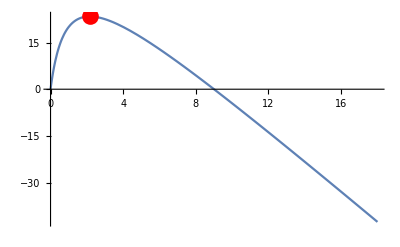

```mathematica
In[1]=Show[Plot[{50x/{x+1}}-5x,{x,0,18}],Graphics[{PointSize[0.03],Red,Point[{2.16228,23.3772}]}]]
```

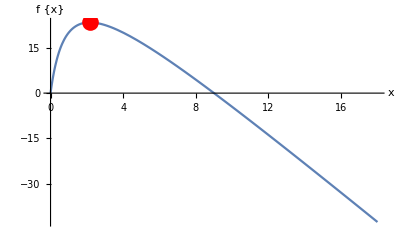

Syntax::sntxf: "Show[" cannot be followed by "[%19,AxesLabel→{HoldForm[x],HoldForm[f«1»]},«1»,LabelStyle→{GrayLevel[0]}],«1»]".

```mathematica
Show[%36,AxesLabel->{HoldForm[x],HoldForm[f {x}]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

Set::write: Tag In in In[2] is Protected.

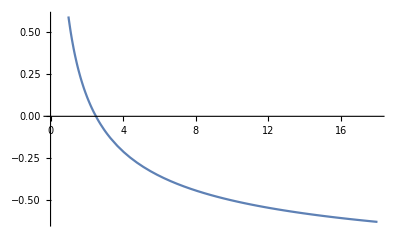

```mathematica
In[2]=Plot[0.5{50/{5d}}^{1/2}-1,{d,0,18}]
```

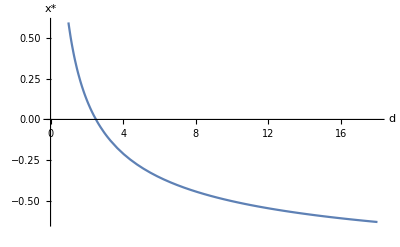

```mathematica
Show[%9,AxesLabel->{HoldForm[d],RawBoxes[RowBox[{"x","*"}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

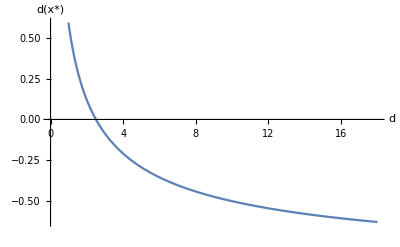

```mathematica
Show[%10,AxesLabel->{HoldForm[d],RawBoxes[RowBox[{RowBox[{"d",RowBox[{"(","x"}]}],"*)"}]]},PlotLabel->None]
```

Set::write: Tag In in In[2] is Protected.

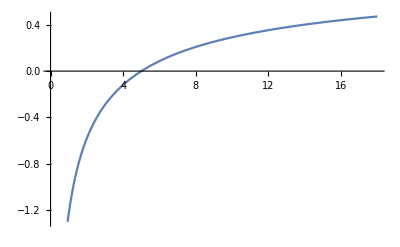

```mathematica
In[2]=Plot[1-{5/V}^0.5,{V,0,18}]
```

```mathematica
In[21]=Plot[{0.5*I}^0.5-I,{I,0,10}]
```

Set::write: Tag In in In[21] is Protected.

-Graphics-

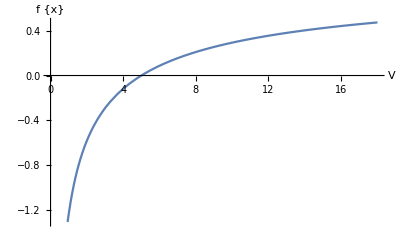

```mathematica
Show[%11,AxesLabel->{HoldForm[V],HoldForm[f {x}]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Show[%12,AxesLabel->{HoldForm[V],RawBoxes[RowBox[{"d",RowBox[{"(",TagBox[RowBox[{RowBox[{"f"," ",RowBox[{"(","x",")"}]}],")"}],HoldForm]}]}]]},PlotLabel->None]
```

Set::write: Tag In in In[3] is Protected.

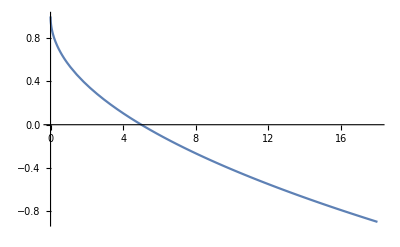

```mathematica
In[3]=Plot[1-{V/5}^0.5,{V,0,18}]
```

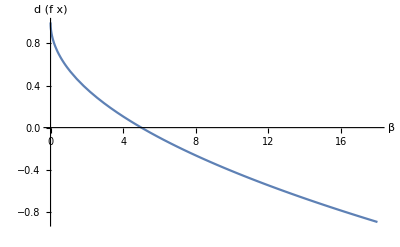

```mathematica
Show[%13,AxesLabel->{HoldForm[β],HoldForm[d (f x)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

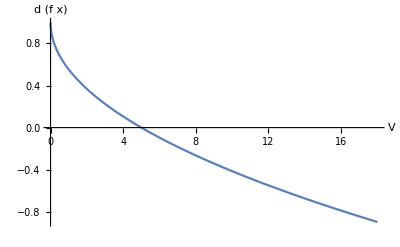

```mathematica
Show[%14,AxesLabel->{HoldForm[V],HoldForm[d (f x)]},PlotLabel->None]
```

```mathematica
In[100]=Show[Plot[{50x/{x+1}}-5x,{x,0,18}]
```

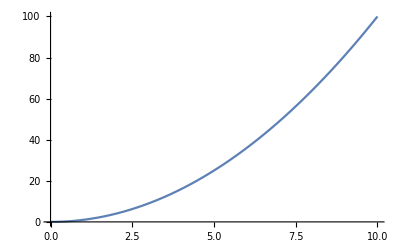

```mathematica
Plot[x=y^2,{y,0,10}]
```

```mathematica
Plot[x=y^2,{y,0,10}]
```